```mathematica
Needs["GraphUtilities`"];
```

```mathematica
g={1->2,3->1,1->4,5->1,1->6,2->3,4->3,3->5,3->6,4->5,5->6,6->7,2->5}
```

{1→2,3→1,1→4,5→1,1→6,2→3,4→3,3→5,3→6,4→5,5→6,6→7,2→5}

```mathematica
gg={1->2,3->1,1->4,5->1,1->6,2->3,4->3,3->5,3->6,4->5,5->6}
```

{1→2,3→1,1→4,5→1,1→6,2→3,4→3,3→5,3→6,4→5,5→6}

```mathematica
AdjacencyMatrix[g]//MatrixForm
```

(0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0)

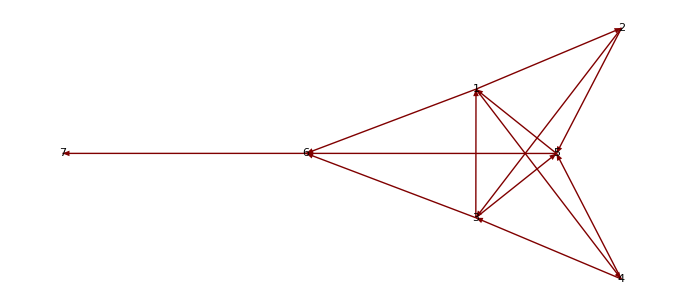

```mathematica
GraphPlot[g,DirectedEdges->True,VertexLabeling->True]
```

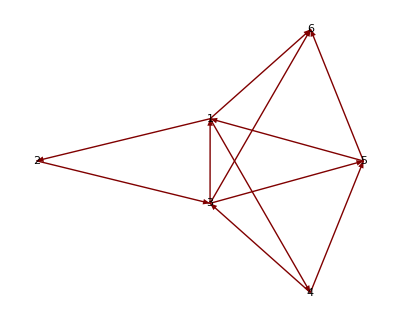

```mathematica
GraphPlot[gg,DirectedEdges->True,VertexLabeling->True]
```

```mathematica
Bicomponents[g]
```

{{6,7},{5,6,4,2,3,1}}

```mathematica
ClosenessCentrality[g]
```

{0.111111,0.0833333,0.111111,0.0833333,0.0909091,0.,0.}

```mathematica
cs=CommunityStructureAssignment[g]
```

{1,1,1,2,1,1,1}

```mathematica
Thread[Rule[VertexList[g],cs]]
```

{1→1,2→1,3→1,4→2,5→1,6→1,7→1}

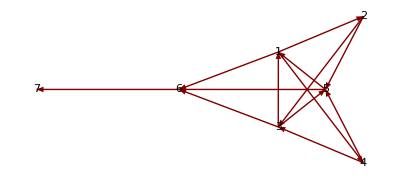

```mathematica
GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({Text[Framed[#2,Background->Hue[cs[[#3]]/4],FrameStyle->RGBColor[0.94,0.85,0.36]],#1]}&)]
```

```mathematica
EdgeList[g]
```

{{1,2},{1,4},{1,6},{2,3},{2,5},{3,1},{3,5},{3,6},{4,3},{4,5},{5,1},{5,6},{6,7}}

```mathematica
g2=Flatten[Map[If[#[[1]]>#[[2]],Rule@@#,{}]&,EdgeList[g]]]
```

{3→1,4→3,5→1}

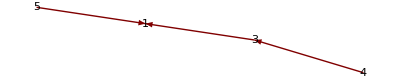

```mathematica
GraphPlot[g2,DirectedEdges->True, VertexLabeling->True]
```

```mathematica
GraphCoordinates[g]
```

{{2.27265,1.04544},{3.07243,1.38192},{2.27173,0.337037},{3.07071,0.},{2.71483,0.691184},{1.339,0.691603},{0.,0.691555}}

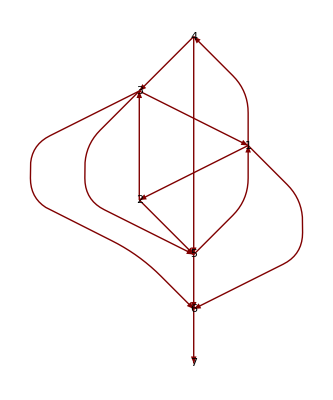

```mathematica
LayeredGraphPlot[g,VertexLabeling->True]
```

```mathematica
GraphDistanceMatrix[g]//MatrixForm
```

(0 | 1 | 2 | 1 | 2 | 1 | 2
2 | 0 | 1 | 3 | 1 | 2 | 3
1 | 2 | 0 | 2 | 1 | 1 | 2
2 | 3 | 1 | 0 | 1 | 2 | 3
1 | 2 | 3 | 2 | 0 | 1 | 2
∞ | ∞ | ∞ | ∞ | ∞ | 0 | 1
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0)

```mathematica
HamiltonianCycles[g,All]
```

{}

```mathematica
MaximalBipartiteMatching[g]
```

{{3,1},{1,2},{2,3},{4,5},{5,6},{6,7}}

```mathematica
match=MaximalIndependentEdgeSet[g]
```

{{1,3},{2,5},{6,7}}

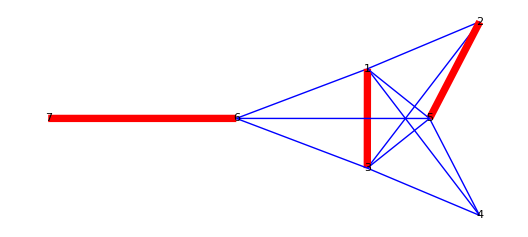

```mathematica
GraphPlot[g,DirectedEdges->True,EdgeRenderingFunction->({If[MemberQ[match,#2]||MemberQ[match,Reverse[#2]],{Red,Thickness[0.01],Line[#]},{Blue,Line[#]}]}&),VertexLabeling->True]
```

```mathematica
m=MaximalIndependentVertexSet[g]
```

{1,7}

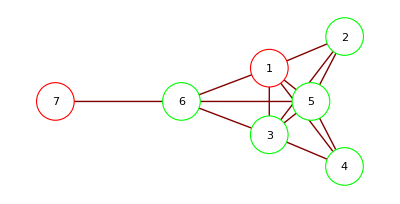

```mathematica
GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({EdgeForm[If[MemberQ[m,#2],Red,Green]],White,Disk[#1,.2],Black,Text[#2,#1]}&)]
```

{{1,6,7},{2,3,4,5}}

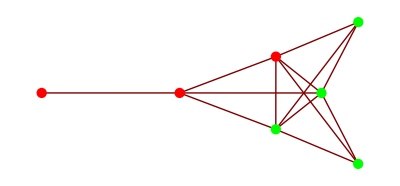

```mathematica
c=MinCut[g,2]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
```

{{6,7},{1,2},{3,4,5}}

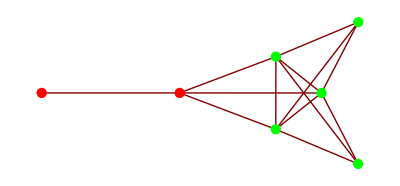

```mathematica
c=MinCut[g,3]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
```

```mathematica
h={1->2,2->3,3->4,4->5,5->6,6->2,2->7,7->3,3->8,8->4,4->9,9->5,5->10,10->6,6->1}
```

{1→2,2→3,3→4,4→5,5→6,6→2,2→7,7→3,3→8,8→4,4→9,9→5,5→10,10→6,6→1}

```mathematica
Needs["GraphUtilities`"];

AdjacencyMatrix[h]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

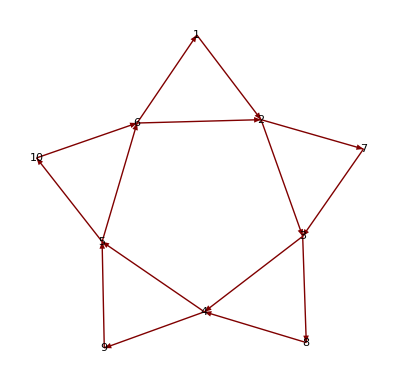

{{5,10,4,9,3,8,2,7,6,1}}

{0.0344828,0.04,0.04,0.04,0.04,0.04,0.0344828,0.0344828,0.0344828,0.0344828}

{1,1,2,2,3,1,2,2,3,3}

{1→1,2→1,3→2,4→2,5→3,6→1,7→2,8→2,9→3,10→3}

-Graphics-

{{1,2},{2,3},{2,7},{3,4},{3,8},{4,5},{4,9},{5,6},{5,10},{6,2},{6,1},{7,3},{8,4},{9,5},{10,6}}

EdgeList::graph: A graph object is expected at position 1 in EdgeList[g].

Part::partd: Part specification g ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification g ⟦ 2 ⟧ is longer than depth of object.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[If[g ⟦ 1 ⟧ > g ⟦ 2 ⟧, Rule @@ g, {}]].

EdgeList[If[g⟦1⟧>g⟦2⟧,Rule@@g,{}]]

GraphPlot::grph: EdgeList[If[g ⟦ 1 ⟧ > g ⟦ 2 ⟧, Rule @@ g, {}]] is not a valid graph.

GraphPlot[EdgeList[If[g⟦1⟧>g⟦2⟧,Rule@@g,{}]],DirectedEdges→True,VertexLabeling→True]

{{1.42338,2.78334},{1.99422,2.03041},{2.36346,0.993133},{1.49029,0.321797},{0.582411,0.945402},{0.892942,2.00054},{2.90324,1.7693},{2.39535,0.0483246},{0.601554,0.},{0.,1.69029}}

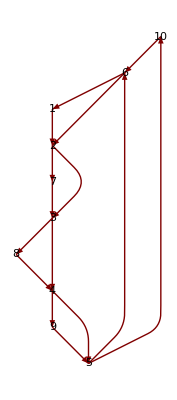

```mathematica
GraphPlot[h,DirectedEdges->True,VertexLabeling->True]

Bicomponents[h]

ClosenessCentrality[h]

cs=CommunityStructureAssignment[h]

Thread[Rule[VertexList[h],cs]]

GraphPlot[h,DirectedEdges->True,VertexRenderingFunction->({Text[Framed[#2,Background->Hue[cs[[#3]]/4],FrameStyle->RGBColor[0.94,0.85,0.36]],#1]}&)]

EdgeList[h]

h2=Flatten[Map[If[#[[1]]>#[[2]],Rule@@#,{}]&,EdgeList[g]]]

GraphPlot[h2,DirectedEdges->True, VertexLabeling->True]

GraphCoordinates[h]

LayeredGraphPlot[h,VertexLabeling->True]
```

```mathematica
GraphDistanceMatrix[h]//MatrixForm
```

(0 | 1 | 2 | 3 | 4 | 5 | 2 | 3 | 4 | 5
5 | 0 | 1 | 2 | 3 | 4 | 1 | 2 | 3 | 4
4 | 4 | 0 | 1 | 2 | 3 | 5 | 1 | 2 | 3
3 | 3 | 4 | 0 | 1 | 2 | 4 | 5 | 1 | 2
2 | 2 | 3 | 4 | 0 | 1 | 3 | 4 | 5 | 1
1 | 1 | 2 | 3 | 4 | 0 | 2 | 3 | 4 | 5
5 | 5 | 1 | 2 | 3 | 4 | 0 | 2 | 3 | 4
4 | 4 | 5 | 1 | 2 | 3 | 5 | 0 | 2 | 3
3 | 3 | 4 | 5 | 1 | 2 | 4 | 5 | 0 | 2
2 | 2 | 3 | 4 | 5 | 1 | 3 | 4 | 5 | 0)

```mathematica
HamiltonianCycles[h,All]
```

{{1,6,10,5,9,4,8,3,7,2},{1,2,7,3,8,4,9,5,10,6}}

{{6,1},{1,2},{7,3},{8,4},{9,5},{10,6},{2,7},{3,8},{4,9},{5,10}}

{{1,2},{3,4},{5,6}}

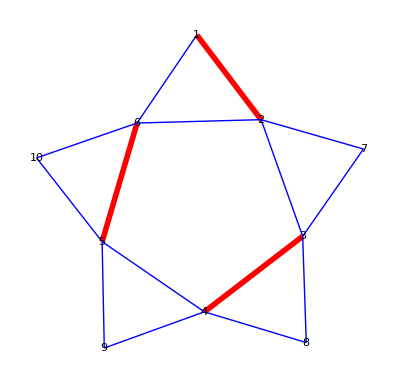

{1,3,5}

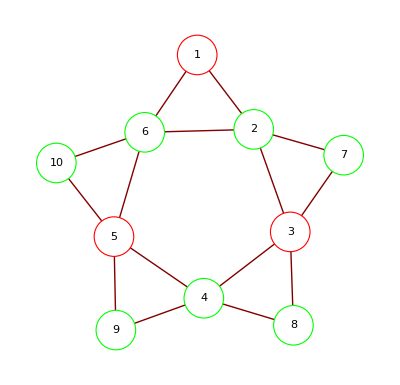

{{3,4,5,8,9},{1,2,6,7,10}}

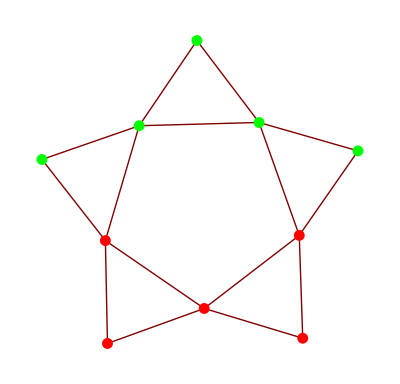

{{4,5,9},{3,7,8},{1,2,6,10}}

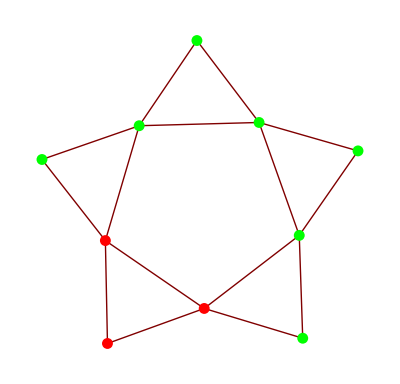

```mathematica
MaximalBipartiteMatching[h]

match=MaximalIndependentEdgeSet[h]

GraphPlot[h,DirectedEdges->True,EdgeRenderingFunction->({If[MemberQ[match,#2]||MemberQ[match,Reverse[#2]],{Red,Thickness[0.01],Line[#]},{Blue,Line[#]}]}&),VertexLabeling->True]

m=MaximalIndependentVertexSet[h]

GraphPlot[h,DirectedEdges->True,VertexRenderingFunction->({EdgeForm[If[MemberQ[m,#2],Red,Green]],White,Disk[#1,.2],Black,Text[#2,#1]}&)]

c=MinCut[h,2]
GraphPlot[h,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]

c=MinCut[h,3]
GraphPlot[h,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
```

```mathematica
Map[ToString,{8,I,R,G,P,Y,A,J,S,C,L,U,B,K,T,F,O,X,H,Q,Z,D,M,V,E,N,W}]
```

```mathematica
let=Partition[{"8","I","R","G","P","Y","A","J","S","C","L","U","B","K","T","F","O","X","H","Q","Z","D","M","V","E","N","W"},3]
```

{{8,I,R},{G,P,Y},{A,J,S},{C,L,U},{B,K,T},{F,O,X},{H,Q,Z},{D,M,V},{E,N,W}}

```mathematica
3^10
```

59049

```mathematica
∑_(i=0)^9 3^i
```

29524

```mathematica
IntegerDigits[29529,3]
```

```mathematica
MemberQ[{1,1,1,1,1,1,1,2,0,0},0]
```

True

```mathematica
let[[1]][[2]]
```

I

```mathematica
DeleteDuplicates[Table[Piecewise[{{let[[i]][[(IntegerDigits[x,3][[i]])]], MemberQ[IntegerDigits[x,3],0]==False}, {0, MemberQ[IntegerDigits[x,3],0]==False}}],{x,29524,59048},{i,1,9}]]//Column
```

{8,G,A,C,B,F,H,D,E}
{0,0,0,0,0,0,0,0,0}
{8,G,A,C,B,F,H,D,N}
{8,G,A,C,B,F,H,M,E}
{8,G,A,C,B,F,H,M,N}
{8,G,A,C,B,F,Q,D,E}
{8,G,A,C,B,F,Q,D,N}
{8,G,A,C,B,F,Q,M,E}
{8,G,A,C,B,F,Q,M,N}
{8,G,A,C,B,O,H,D,E}
{8,G,A,C,B,O,H,D,N}
{8,G,A,C,B,O,H,M,E}
{8,G,A,C,B,O,H,M,N}
{8,G,A,C,B,O,Q,D,E}
{8,G,A,C,B,O,Q,D,N}
{8,G,A,C,B,O,Q,M,E}
{8,G,A,C,B,O,Q,M,N}
{8,G,A,C,K,F,H,D,E}
{8,G,A,C,K,F,H,D,N}
{8,G,A,C,K,F,H,M,E}
{8,G,A,C,K,F,H,M,N}
{8,G,A,C,K,F,Q,D,E}
{8,G,A,C,K,F,Q,D,N}
{8,G,A,C,K,F,Q,M,E}
{8,G,A,C,K,F,Q,M,N}
{8,G,A,C,K,O,H,D,E}
{8,G,A,C,K,O,H,D,N}
{8,G,A,C,K,O,H,M,E}
{8,G,A,C,K,O,H,M,N}
{8,G,A,C,K,O,Q,D,E}
{8,G,A,C,K,O,Q,D,N}
{8,G,A,C,K,O,Q,M,E}
{8,G,A,C,K,O,Q,M,N}
{8,G,A,L,B,F,H,D,E}
{8,G,A,L,B,F,H,D,N}
{8,G,A,L,B,F,H,M,E}
{8,G,A,L,B,F,H,M,N}
{8,G,A,L,B,F,Q,D,E}
{8,G,A,L,B,F,Q,D,N}
{8,G,A,L,B,F,Q,M,E}
{8,G,A,L,B,F,Q,M,N}
{8,G,A,L,B,O,H,D,E}
{8,G,A,L,B,O,H,D,N}
{8,G,A,L,B,O,H,M,E}
{8,G,A,L,B,O,H,M,N}
{8,G,A,L,B,O,Q,D,E}
{8,G,A,L,B,O,Q,D,N}
{8,G,A,L,B,O,Q,M,E}
{8,G,A,L,B,O,Q,M,N}
{8,G,A,L,K,F,H,D,E}
{8,G,A,L,K,F,H,D,N}
{8,G,A,L,K,F,H,M,E}
{8,G,A,L,K,F,H,M,N}
{8,G,A,L,K,F,Q,D,E}
{8,G,A,L,K,F,Q,D,N}
{8,G,A,L,K,F,Q,M,E}
{8,G,A,L,K,F,Q,M,N}
{8,G,A,L,K,O,H,D,E}
{8,G,A,L,K,O,H,D,N}
{8,G,A,L,K,O,H,M,E}
{8,G,A,L,K,O,H,M,N}
{8,G,A,L,K,O,Q,D,E}
{8,G,A,L,K,O,Q,D,N}
{8,G,A,L,K,O,Q,M,E}
{8,G,A,L,K,O,Q,M,N}
{8,G,J,C,B,F,H,D,E}
{8,G,J,C,B,F,H,D,N}
{8,G,J,C,B,F,H,M,E}
{8,G,J,C,B,F,H,M,N}
{8,G,J,C,B,F,Q,D,E}
{8,G,J,C,B,F,Q,D,N}
{8,G,J,C,B,F,Q,M,E}
{8,G,J,C,B,F,Q,M,N}
{8,G,J,C,B,O,H,D,E}
{8,G,J,C,B,O,H,D,N}
{8,G,J,C,B,O,H,M,E}
{8,G,J,C,B,O,H,M,N}
{8,G,J,C,B,O,Q,D,E}
{8,G,J,C,B,O,Q,D,N}
{8,G,J,C,B,O,Q,M,E}
{8,G,J,C,B,O,Q,M,N}
{8,G,J,C,K,F,H,D,E}
{8,G,J,C,K,F,H,D,N}
{8,G,J,C,K,F,H,M,E}
{8,G,J,C,K,F,H,M,N}
{8,G,J,C,K,F,Q,D,E}
{8,G,J,C,K,F,Q,D,N}
{8,G,J,C,K,F,Q,M,E}
{8,G,J,C,K,F,Q,M,N}
{8,G,J,C,K,O,H,D,E}
{8,G,J,C,K,O,H,D,N}
{8,G,J,C,K,O,H,M,E}
{8,G,J,C,K,O,H,M,N}
{8,G,J,C,K,O,Q,D,E}
{8,G,J,C,K,O,Q,D,N}
{8,G,J,C,K,O,Q,M,E}
{8,G,J,C,K,O,Q,M,N}
{8,G,J,L,B,F,H,D,E}
{8,G,J,L,B,F,H,D,N}
{8,G,J,L,B,F,H,M,E}
{8,G,J,L,B,F,H,M,N}
{8,G,J,L,B,F,Q,D,E}
{8,G,J,L,B,F,Q,D,N}
{8,G,J,L,B,F,Q,M,E}
{8,G,J,L,B,F,Q,M,N}
{8,G,J,L,B,O,H,D,E}
{8,G,J,L,B,O,H,D,N}
{8,G,J,L,B,O,H,M,E}
{8,G,J,L,B,O,H,M,N}
{8,G,J,L,B,O,Q,D,E}
{8,G,J,L,B,O,Q,D,N}
{8,G,J,L,B,O,Q,M,E}
{8,G,J,L,B,O,Q,M,N}
{8,G,J,L,K,F,H,D,E}
{8,G,J,L,K,F,H,D,N}
{8,G,J,L,K,F,H,M,E}
{8,G,J,L,K,F,H,M,N}
{8,G,J,L,K,F,Q,D,E}
{8,G,J,L,K,F,Q,D,N}
{8,G,J,L,K,F,Q,M,E}
{8,G,J,L,K,F,Q,M,N}
{8,G,J,L,K,O,H,D,E}
{8,G,J,L,K,O,H,D,N}
{8,G,J,L,K,O,H,M,E}
{8,G,J,L,K,O,H,M,N}
{8,G,J,L,K,O,Q,D,E}
{8,G,J,L,K,O,Q,D,N}
{8,G,J,L,K,O,Q,M,E}
{8,G,J,L,K,O,Q,M,N}
{8,P,A,C,B,F,H,D,E}
{8,P,A,C,B,F,H,D,N}
{8,P,A,C,B,F,H,M,E}
{8,P,A,C,B,F,H,M,N}
{8,P,A,C,B,F,Q,D,E}
{8,P,A,C,B,F,Q,D,N}
{8,P,A,C,B,F,Q,M,E}
{8,P,A,C,B,F,Q,M,N}
{8,P,A,C,B,O,H,D,E}
{8,P,A,C,B,O,H,D,N}
{8,P,A,C,B,O,H,M,E}
{8,P,A,C,B,O,H,M,N}
{8,P,A,C,B,O,Q,D,E}
{8,P,A,C,B,O,Q,D,N}
{8,P,A,C,B,O,Q,M,E}
{8,P,A,C,B,O,Q,M,N}
{8,P,A,C,K,F,H,D,E}
{8,P,A,C,K,F,H,D,N}
{8,P,A,C,K,F,H,M,E}
{8,P,A,C,K,F,H,M,N}
{8,P,A,C,K,F,Q,D,E}
{8,P,A,C,K,F,Q,D,N}
{8,P,A,C,K,F,Q,M,E}
{8,P,A,C,K,F,Q,M,N}
{8,P,A,C,K,O,H,D,E}
{8,P,A,C,K,O,H,D,N}
{8,P,A,C,K,O,H,M,E}
{8,P,A,C,K,O,H,M,N}
{8,P,A,C,K,O,Q,D,E}
{8,P,A,C,K,O,Q,D,N}
{8,P,A,C,K,O,Q,M,E}
{8,P,A,C,K,O,Q,M,N}
{8,P,A,L,B,F,H,D,E}
{8,P,A,L,B,F,H,D,N}
{8,P,A,L,B,F,H,M,E}
{8,P,A,L,B,F,H,M,N}
{8,P,A,L,B,F,Q,D,E}
{8,P,A,L,B,F,Q,D,N}
{8,P,A,L,B,F,Q,M,E}
{8,P,A,L,B,F,Q,M,N}
{8,P,A,L,B,O,H,D,E}
{8,P,A,L,B,O,H,D,N}
{8,P,A,L,B,O,H,M,E}
{8,P,A,L,B,O,H,M,N}
{8,P,A,L,B,O,Q,D,E}
{8,P,A,L,B,O,Q,D,N}
{8,P,A,L,B,O,Q,M,E}
{8,P,A,L,B,O,Q,M,N}
{8,P,A,L,K,F,H,D,E}
{8,P,A,L,K,F,H,D,N}
{8,P,A,L,K,F,H,M,E}
{8,P,A,L,K,F,H,M,N}
{8,P,A,L,K,F,Q,D,E}
{8,P,A,L,K,F,Q,D,N}
{8,P,A,L,K,F,Q,M,E}
{8,P,A,L,K,F,Q,M,N}
{8,P,A,L,K,O,H,D,E}
{8,P,A,L,K,O,H,D,N}
{8,P,A,L,K,O,H,M,E}
{8,P,A,L,K,O,H,M,N}
{8,P,A,L,K,O,Q,D,E}
{8,P,A,L,K,O,Q,D,N}
{8,P,A,L,K,O,Q,M,E}
{8,P,A,L,K,O,Q,M,N}
{8,P,J,C,B,F,H,D,E}
{8,P,J,C,B,F,H,D,N}
{8,P,J,C,B,F,H,M,E}
{8,P,J,C,B,F,H,M,N}
{8,P,J,C,B,F,Q,D,E}
{8,P,J,C,B,F,Q,D,N}
{8,P,J,C,B,F,Q,M,E}
{8,P,J,C,B,F,Q,M,N}
{8,P,J,C,B,O,H,D,E}
{8,P,J,C,B,O,H,D,N}
{8,P,J,C,B,O,H,M,E}
{8,P,J,C,B,O,H,M,N}
{8,P,J,C,B,O,Q,D,E}
{8,P,J,C,B,O,Q,D,N}
{8,P,J,C,B,O,Q,M,E}
{8,P,J,C,B,O,Q,M,N}
{8,P,J,C,K,F,H,D,E}
{8,P,J,C,K,F,H,D,N}
{8,P,J,C,K,F,H,M,E}
{8,P,J,C,K,F,H,M,N}
{8,P,J,C,K,F,Q,D,E}
{8,P,J,C,K,F,Q,D,N}
{8,P,J,C,K,F,Q,M,E}
{8,P,J,C,K,F,Q,M,N}
{8,P,J,C,K,O,H,D,E}
{8,P,J,C,K,O,H,D,N}
{8,P,J,C,K,O,H,M,E}
{8,P,J,C,K,O,H,M,N}
{8,P,J,C,K,O,Q,D,E}
{8,P,J,C,K,O,Q,D,N}
{8,P,J,C,K,O,Q,M,E}
{8,P,J,C,K,O,Q,M,N}
{8,P,J,L,B,F,H,D,E}
{8,P,J,L,B,F,H,D,N}
{8,P,J,L,B,F,H,M,E}
{8,P,J,L,B,F,H,M,N}
{8,P,J,L,B,F,Q,D,E}
{8,P,J,L,B,F,Q,D,N}
{8,P,J,L,B,F,Q,M,E}
{8,P,J,L,B,F,Q,M,N}
{8,P,J,L,B,O,H,D,E}
{8,P,J,L,B,O,H,D,N}
{8,P,J,L,B,O,H,M,E}
{8,P,J,L,B,O,H,M,N}
{8,P,J,L,B,O,Q,D,E}
{8,P,J,L,B,O,Q,D,N}
{8,P,J,L,B,O,Q,M,E}
{8,P,J,L,B,O,Q,M,N}
{8,P,J,L,K,F,H,D,E}
{8,P,J,L,K,F,H,D,N}
{8,P,J,L,K,F,H,M,E}
{8,P,J,L,K,F,H,M,N}
{8,P,J,L,K,F,Q,D,E}
{8,P,J,L,K,F,Q,D,N}
{8,P,J,L,K,F,Q,M,E}
{8,P,J,L,K,F,Q,M,N}
{8,P,J,L,K,O,H,D,E}
{8,P,J,L,K,O,H,D,N}
{8,P,J,L,K,O,H,M,E}
{8,P,J,L,K,O,H,M,N}
{8,P,J,L,K,O,Q,D,E}
{8,P,J,L,K,O,Q,D,N}
{8,P,J,L,K,O,Q,M,E}
{8,P,J,L,K,O,Q,M,N}
{I,G,A,C,B,F,H,D,E}
{I,G,A,C,B,F,H,D,N}
{I,G,A,C,B,F,H,M,E}
{I,G,A,C,B,F,H,M,N}
{I,G,A,C,B,F,Q,D,E}
{I,G,A,C,B,F,Q,D,N}
{I,G,A,C,B,F,Q,M,E}
{I,G,A,C,B,F,Q,M,N}
{I,G,A,C,B,O,H,D,E}
{I,G,A,C,B,O,H,D,N}
{I,G,A,C,B,O,H,M,E}
{I,G,A,C,B,O,H,M,N}
{I,G,A,C,B,O,Q,D,E}
{I,G,A,C,B,O,Q,D,N}
{I,G,A,C,B,O,Q,M,E}
{I,G,A,C,B,O,Q,M,N}
{I,G,A,C,K,F,H,D,E}
{I,G,A,C,K,F,H,D,N}
{I,G,A,C,K,F,H,M,E}
{I,G,A,C,K,F,H,M,N}
{I,G,A,C,K,F,Q,D,E}
{I,G,A,C,K,F,Q,D,N}
{I,G,A,C,K,F,Q,M,E}
{I,G,A,C,K,F,Q,M,N}
{I,G,A,C,K,O,H,D,E}
{I,G,A,C,K,O,H,D,N}
{I,G,A,C,K,O,H,M,E}
{I,G,A,C,K,O,H,M,N}
{I,G,A,C,K,O,Q,D,E}
{I,G,A,C,K,O,Q,D,N}
{I,G,A,C,K,O,Q,M,E}
{I,G,A,C,K,O,Q,M,N}
{I,G,A,L,B,F,H,D,E}
{I,G,A,L,B,F,H,D,N}
{I,G,A,L,B,F,H,M,E}
{I,G,A,L,B,F,H,M,N}
{I,G,A,L,B,F,Q,D,E}
{I,G,A,L,B,F,Q,D,N}
{I,G,A,L,B,F,Q,M,E}
{I,G,A,L,B,F,Q,M,N}
{I,G,A,L,B,O,H,D,E}
{I,G,A,L,B,O,H,D,N}
{I,G,A,L,B,O,H,M,E}
{I,G,A,L,B,O,H,M,N}
{I,G,A,L,B,O,Q,D,E}
{I,G,A,L,B,O,Q,D,N}
{I,G,A,L,B,O,Q,M,E}
{I,G,A,L,B,O,Q,M,N}
{I,G,A,L,K,F,H,D,E}
{I,G,A,L,K,F,H,D,N}
{I,G,A,L,K,F,H,M,E}
{I,G,A,L,K,F,H,M,N}
{I,G,A,L,K,F,Q,D,E}
{I,G,A,L,K,F,Q,D,N}
{I,G,A,L,K,F,Q,M,E}
{I,G,A,L,K,F,Q,M,N}
{I,G,A,L,K,O,H,D,E}
{I,G,A,L,K,O,H,D,N}
{I,G,A,L,K,O,H,M,E}
{I,G,A,L,K,O,H,M,N}
{I,G,A,L,K,O,Q,D,E}
{I,G,A,L,K,O,Q,D,N}
{I,G,A,L,K,O,Q,M,E}
{I,G,A,L,K,O,Q,M,N}
{I,G,J,C,B,F,H,D,E}
{I,G,J,C,B,F,H,D,N}
{I,G,J,C,B,F,H,M,E}
{I,G,J,C,B,F,H,M,N}
{I,G,J,C,B,F,Q,D,E}
{I,G,J,C,B,F,Q,D,N}
{I,G,J,C,B,F,Q,M,E}
{I,G,J,C,B,F,Q,M,N}
{I,G,J,C,B,O,H,D,E}
{I,G,J,C,B,O,H,D,N}
{I,G,J,C,B,O,H,M,E}
{I,G,J,C,B,O,H,M,N}
{I,G,J,C,B,O,Q,D,E}
{I,G,J,C,B,O,Q,D,N}
{I,G,J,C,B,O,Q,M,E}
{I,G,J,C,B,O,Q,M,N}
{I,G,J,C,K,F,H,D,E}
{I,G,J,C,K,F,H,D,N}
{I,G,J,C,K,F,H,M,E}
{I,G,J,C,K,F,H,M,N}
{I,G,J,C,K,F,Q,D,E}
{I,G,J,C,K,F,Q,D,N}
{I,G,J,C,K,F,Q,M,E}
{I,G,J,C,K,F,Q,M,N}
{I,G,J,C,K,O,H,D,E}
{I,G,J,C,K,O,H,D,N}
{I,G,J,C,K,O,H,M,E}
{I,G,J,C,K,O,H,M,N}
{I,G,J,C,K,O,Q,D,E}
{I,G,J,C,K,O,Q,D,N}
{I,G,J,C,K,O,Q,M,E}
{I,G,J,C,K,O,Q,M,N}
{I,G,J,L,B,F,H,D,E}
{I,G,J,L,B,F,H,D,N}
{I,G,J,L,B,F,H,M,E}
{I,G,J,L,B,F,H,M,N}
{I,G,J,L,B,F,Q,D,E}
{I,G,J,L,B,F,Q,D,N}
{I,G,J,L,B,F,Q,M,E}
{I,G,J,L,B,F,Q,M,N}
{I,G,J,L,B,O,H,D,E}
{I,G,J,L,B,O,H,D,N}
{I,G,J,L,B,O,H,M,E}
{I,G,J,L,B,O,H,M,N}
{I,G,J,L,B,O,Q,D,E}
{I,G,J,L,B,O,Q,D,N}
{I,G,J,L,B,O,Q,M,E}
{I,G,J,L,B,O,Q,M,N}
{I,G,J,L,K,F,H,D,E}
{I,G,J,L,K,F,H,D,N}
{I,G,J,L,K,F,H,M,E}
{I,G,J,L,K,F,H,M,N}
{I,G,J,L,K,F,Q,D,E}
{I,G,J,L,K,F,Q,D,N}
{I,G,J,L,K,F,Q,M,E}
{I,G,J,L,K,F,Q,M,N}
{I,G,J,L,K,O,H,D,E}
{I,G,J,L,K,O,H,D,N}
{I,G,J,L,K,O,H,M,E}
{I,G,J,L,K,O,H,M,N}
{I,G,J,L,K,O,Q,D,E}
{I,G,J,L,K,O,Q,D,N}
{I,G,J,L,K,O,Q,M,E}
{I,G,J,L,K,O,Q,M,N}
{I,P,A,C,B,F,H,D,E}
{I,P,A,C,B,F,H,D,N}
{I,P,A,C,B,F,H,M,E}
{I,P,A,C,B,F,H,M,N}
{I,P,A,C,B,F,Q,D,E}
{I,P,A,C,B,F,Q,D,N}
{I,P,A,C,B,F,Q,M,E}
{I,P,A,C,B,F,Q,M,N}
{I,P,A,C,B,O,H,D,E}
{I,P,A,C,B,O,H,D,N}
{I,P,A,C,B,O,H,M,E}
{I,P,A,C,B,O,H,M,N}
{I,P,A,C,B,O,Q,D,E}
{I,P,A,C,B,O,Q,D,N}
{I,P,A,C,B,O,Q,M,E}
{I,P,A,C,B,O,Q,M,N}
{I,P,A,C,K,F,H,D,E}
{I,P,A,C,K,F,H,D,N}
{I,P,A,C,K,F,H,M,E}
{I,P,A,C,K,F,H,M,N}
{I,P,A,C,K,F,Q,D,E}
{I,P,A,C,K,F,Q,D,N}
{I,P,A,C,K,F,Q,M,E}
{I,P,A,C,K,F,Q,M,N}
{I,P,A,C,K,O,H,D,E}
{I,P,A,C,K,O,H,D,N}
{I,P,A,C,K,O,H,M,E}
{I,P,A,C,K,O,H,M,N}
{I,P,A,C,K,O,Q,D,E}
{I,P,A,C,K,O,Q,D,N}
{I,P,A,C,K,O,Q,M,E}
{I,P,A,C,K,O,Q,M,N}
{I,P,A,L,B,F,H,D,E}
{I,P,A,L,B,F,H,D,N}
{I,P,A,L,B,F,H,M,E}
{I,P,A,L,B,F,H,M,N}
{I,P,A,L,B,F,Q,D,E}
{I,P,A,L,B,F,Q,D,N}
{I,P,A,L,B,F,Q,M,E}
{I,P,A,L,B,F,Q,M,N}
{I,P,A,L,B,O,H,D,E}
{I,P,A,L,B,O,H,D,N}
{I,P,A,L,B,O,H,M,E}
{I,P,A,L,B,O,H,M,N}
{I,P,A,L,B,O,Q,D,E}
{I,P,A,L,B,O,Q,D,N}
{I,P,A,L,B,O,Q,M,E}
{I,P,A,L,B,O,Q,M,N}
{I,P,A,L,K,F,H,D,E}
{I,P,A,L,K,F,H,D,N}
{I,P,A,L,K,F,H,M,E}
{I,P,A,L,K,F,H,M,N}
{I,P,A,L,K,F,Q,D,E}
{I,P,A,L,K,F,Q,D,N}
{I,P,A,L,K,F,Q,M,E}
{I,P,A,L,K,F,Q,M,N}
{I,P,A,L,K,O,H,D,E}
{I,P,A,L,K,O,H,D,N}
{I,P,A,L,K,O,H,M,E}
{I,P,A,L,K,O,H,M,N}
{I,P,A,L,K,O,Q,D,E}
{I,P,A,L,K,O,Q,D,N}
{I,P,A,L,K,O,Q,M,E}
{I,P,A,L,K,O,Q,M,N}
{I,P,J,C,B,F,H,D,E}
{I,P,J,C,B,F,H,D,N}
{I,P,J,C,B,F,H,M,E}
{I,P,J,C,B,F,H,M,N}
{I,P,J,C,B,F,Q,D,E}
{I,P,J,C,B,F,Q,D,N}
{I,P,J,C,B,F,Q,M,E}
{I,P,J,C,B,F,Q,M,N}
{I,P,J,C,B,O,H,D,E}
{I,P,J,C,B,O,H,D,N}
{I,P,J,C,B,O,H,M,E}
{I,P,J,C,B,O,H,M,N}
{I,P,J,C,B,O,Q,D,E}
{I,P,J,C,B,O,Q,D,N}
{I,P,J,C,B,O,Q,M,E}
{I,P,J,C,B,O,Q,M,N}
{I,P,J,C,K,F,H,D,E}
{I,P,J,C,K,F,H,D,N}
{I,P,J,C,K,F,H,M,E}
{I,P,J,C,K,F,H,M,N}
{I,P,J,C,K,F,Q,D,E}
{I,P,J,C,K,F,Q,D,N}
{I,P,J,C,K,F,Q,M,E}
{I,P,J,C,K,F,Q,M,N}
{I,P,J,C,K,O,H,D,E}
{I,P,J,C,K,O,H,D,N}
{I,P,J,C,K,O,H,M,E}
{I,P,J,C,K,O,H,M,N}
{I,P,J,C,K,O,Q,D,E}
{I,P,J,C,K,O,Q,D,N}
{I,P,J,C,K,O,Q,M,E}
{I,P,J,C,K,O,Q,M,N}
{I,P,J,L,B,F,H,D,E}
{I,P,J,L,B,F,H,D,N}
{I,P,J,L,B,F,H,M,E}
{I,P,J,L,B,F,H,M,N}
{I,P,J,L,B,F,Q,D,E}
{I,P,J,L,B,F,Q,D,N}
{I,P,J,L,B,F,Q,M,E}
{I,P,J,L,B,F,Q,M,N}
{I,P,J,L,B,O,H,D,E}
{I,P,J,L,B,O,H,D,N}
{I,P,J,L,B,O,H,M,E}
{I,P,J,L,B,O,H,M,N}
{I,P,J,L,B,O,Q,D,E}
{I,P,J,L,B,O,Q,D,N}
{I,P,J,L,B,O,Q,M,E}
{I,P,J,L,B,O,Q,M,N}
{I,P,J,L,K,F,H,D,E}
{I,P,J,L,K,F,H,D,N}
{I,P,J,L,K,F,H,M,E}
{I,P,J,L,K,F,H,M,N}
{I,P,J,L,K,F,Q,D,E}
{I,P,J,L,K,F,Q,D,N}
{I,P,J,L,K,F,Q,M,E}
{I,P,J,L,K,F,Q,M,N}
{I,P,J,L,K,O,H,D,E}
{I,P,J,L,K,O,H,D,N}
{I,P,J,L,K,O,H,M,E}
{I,P,J,L,K,O,H,M,N}
{I,P,J,L,K,O,Q,D,E}
{I,P,J,L,K,O,Q,D,N}
{I,P,J,L,K,O,Q,M,E}
{I,P,J,L,K,O,Q,M,N}

```mathematica
StringJoin[{"I","P","A","L","B","O","H","M","E"}]
```

IPALBOHME

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→2,2→9,9→10,10→3,3→8,8→11,11→2,2→10,10→12,12→4,4→6,6→13,13→5,5→14}

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→2,2→9,9→10,10→3,3→8,8→11,11→2,2→10,10→12,12→4,4→6,6→13,13→5,5→1}

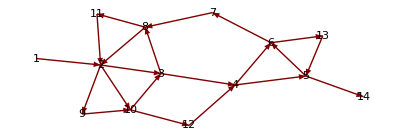

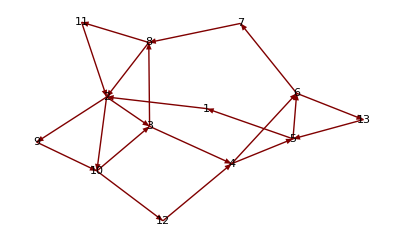

```mathematica
Needs["GraphUtilities`"];
g={1->2,2->3,3->4, 4->5,5->6,6->7,7->8, 8->2, 2->9, 9->10, 10->3, 3->8, 8->11, 11->2, 2->10, 10->12, 12->4, 4->6, 6->13, 13->5, 5->14}
gg ={1->2,2->3,3->4, 4->5,5->6,6->7,7->8, 8->2, 2->9, 9->10, 10->3, 3->8, 8->11, 11->2, 2->10, 10->12, 12->4, 4->6, 6->13, 13->5, 5->1}

GraphPlot[g,DirectedEdges->True,VertexLabeling->True]

GraphPlot[gg,DirectedEdges->True,VertexLabeling->True]
```

```mathematica
AdjacencyMatrix[g]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

{{10,12,9,2,8,11,6,13,7,3,4,5,1}}

{0.0263158,0.0333333,0.0344828,0.0285714,0.03125,0.027027,0.0227273,0.027027,0.0238095,0.0294118,0.025641,0.0238095,0.0238095}

{1,2,2,1,1,1,1,2,2,2,2,1,1}

{1→1,2→2,3→2,4→1,5→1,6→1,7→1,8→2,9→2,10→2,11→2,12→1,13→1}

-Graphics-

{{1,2},{2,3},{2,9},{2,10},{3,4},{3,8},{4,5},{4,6},{5,6},{5,1},{6,7},{6,13},{7,8},{8,2},{8,11},{9,10},{10,3},{10,12},{11,2},{12,4},{13,5}}

{5→1,8→2,10→3,11→2,12→4,13→5}

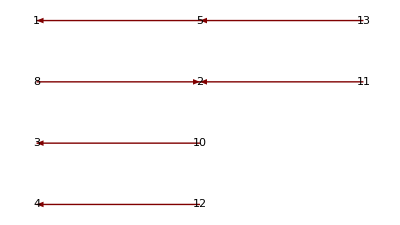

{{2.14463,1.4195},{0.883037,1.56672},{1.42483,1.19514},{2.45928,0.722543},{3.23189,1.0372},{3.27841,1.6134},{2.57044,2.49758},{1.41466,2.2564},{0.,0.996013},{0.760483,0.63093},{0.56754,2.51305},{1.5935,0.},{4.12008,1.28033}}

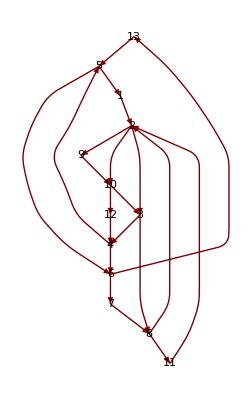

(0 | 1 | 2 | 3 | 4 | 4 | 5 | 3 | 2 | 2 | 4 | 3 | 5
4 | 0 | 1 | 2 | 3 | 3 | 4 | 2 | 1 | 1 | 3 | 2 | 4
3 | 2 | 0 | 1 | 2 | 2 | 3 | 1 | 3 | 3 | 2 | 4 | 3
2 | 3 | 4 | 0 | 1 | 1 | 2 | 3 | 4 | 4 | 4 | 5 | 2
1 | 2 | 3 | 4 | 0 | 1 | 2 | 3 | 3 | 3 | 4 | 4 | 2
3 | 3 | 4 | 5 | 2 | 0 | 1 | 2 | 4 | 4 | 3 | 5 | 1
6 | 2 | 3 | 4 | 5 | 5 | 0 | 1 | 3 | 3 | 2 | 4 | 6
5 | 1 | 2 | 3 | 4 | 4 | 5 | 0 | 2 | 2 | 1 | 3 | 5
5 | 4 | 2 | 3 | 4 | 4 | 5 | 3 | 0 | 1 | 4 | 2 | 5
4 | 3 | 1 | 2 | 3 | 3 | 4 | 2 | 4 | 0 | 3 | 1 | 4
5 | 1 | 2 | 3 | 4 | 4 | 5 | 3 | 2 | 2 | 0 | 3 | 5
3 | 4 | 5 | 1 | 2 | 2 | 3 | 4 | 5 | 5 | 5 | 0 | 3
2 | 3 | 4 | 5 | 1 | 2 | 3 | 4 | 4 | 4 | 5 | 5 | 0)

{}

{{5,1},{1,2},{2,3},{3,4},{13,5},{4,6},{6,7},{7,8},{9,10},{8,11},{10,12}}

{{1,2},{3,4},{5,6},{7,8},{9,10}}

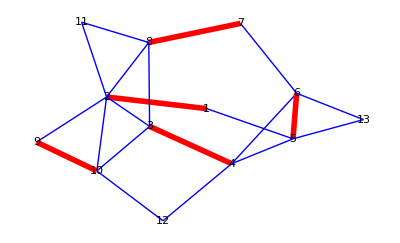

{1,3,6,9,11,12}

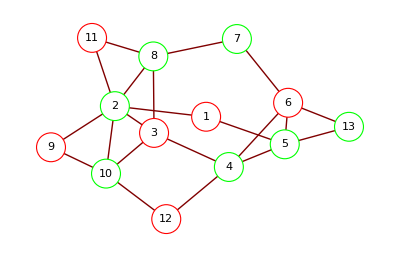

{{1,4,5,6,7,13},{2,3,8,9,10,11,12}}

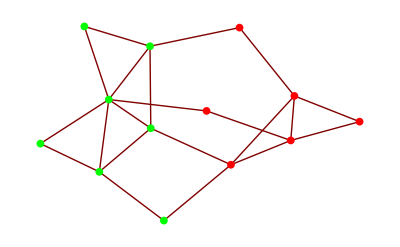

{{1,6,7},{2,3,4,5}}

{{4,5,6,13},{1,9,10,12},{2,3,7,8,11}}

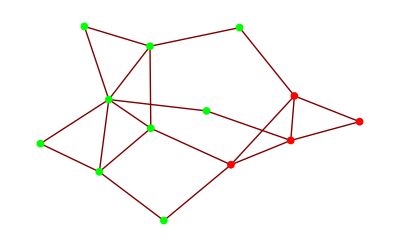

{{6,7},{1,2},{3,4,5}}

{1→2,2→3,3→4,4→5,5→6,6→2,2→7,7→3,3→8,8→4,4→9,9→5,5→10,10→6,6→1}

```mathematica
Bicomponents[g]

ClosenessCentrality[g]

cs=CommunityStructureAssignment[g]

Thread[Rule[VertexList[g],cs]]

GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({Text[Framed[#2,Background->Hue[cs[[#3]]/4],FrameStyle->RGBColor[0.94,0.85,0.36]],#1]}&)]

EdgeList[g]

g2=Flatten[Map[If[#[[1]]>#[[2]],Rule@@#,{}]&,EdgeList[g]]]

GraphPlot[g2,DirectedEdges->True, VertexLabeling->True]

GraphCoordinates[g]

LayeredGraphPlot[g,VertexLabeling->True]

GraphDistanceMatrix[g]//MatrixForm

HamiltonianCycles[g,All]

MaximalBipartiteMatching[g]

match=MaximalIndependentEdgeSet[g]

GraphPlot[g,DirectedEdges->True,EdgeRenderingFunction->({If[MemberQ[match,#2]||MemberQ[match,Reverse[#2]],{Red,Thickness[0.01],Line[#]},{Blue,Line[#]}]}&),VertexLabeling->True]
m=MaximalIndependentVertexSet[g]

GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({EdgeForm[If[MemberQ[m,#2],Red,Green]],White,Disk[#1,.2],Black,Text[#2,#1]}&)]
c=MinCut[g,2]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
{{1,6,7},{2,3,4,5}}
c=MinCut[g,3]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
{{6,7},{1,2},{3,4,5}}
h={1->2,2->3,3->4,4->5,5->6,6->2,2->7,7->3,3->8,8->4,4->9,9->5,5->10,10->6,6->1}
```

```mathematica
g={1->2,2->3,3->4,4->5,5->2,2->5,5->3,3->4,4->6}
```

{1→2,2→3,3→4,4→5,5→2,2→5,5→3,3→4,4→6}

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

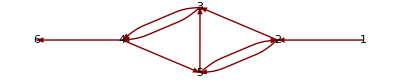

GraphPlot::grph: gg is not a valid graph.

GraphPlot[gg,DirectedEdges→True,VertexLabeling→True]

{{4,6},{4,3,5,2},{1,2}}

{0.0714286,0.,0.,0.,0.,0.}

{1,2,2,3,2,3}

{1→1,2→2,3→2,4→3,5→2,6→3}

-Graphics-

{{1,2},{2,3},{2,5},{3,4},{4,5},{4,6},{5,2},{5,3}}

{5→2,5→3}

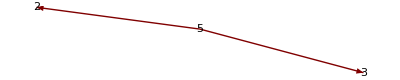

{{4.11415,0.325909},{3.03261,0.325848},{2.05716,0.652708},{1.08051,0.326262},{2.05584,0.},{0.,0.325922}}

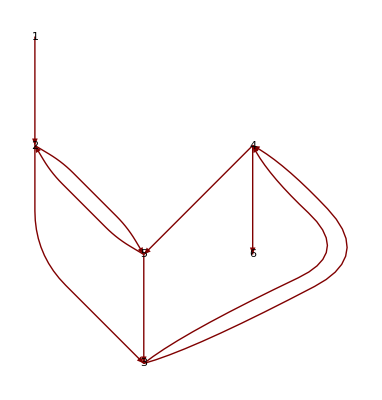

(0 | 1 | 2 | 4 | 2 | 5
∞ | 0 | 1 | 3 | 1 | 4
∞ | 4 | 0 | 2 | 3 | 3
∞ | 2 | 2 | 0 | 1 | 1
∞ | 1 | 1 | 3 | 0 | 4
∞ | ∞ | ∞ | ∞ | ∞ | 0)

{}

{{1,2},{5,3},{3,4},{2,5},{4,6}}

{{1,2},{3,5},{4,6}}

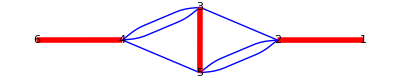

{1,3,6}

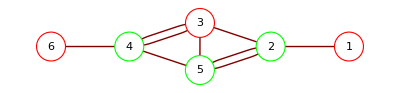

{{1,2,5},{3,4,6}}

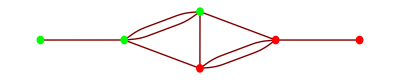

{{1,2},{3,5},{4,6}}

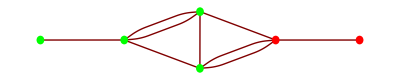

```mathematica
Needs["GraphUtilities`"];
AdjacencyMatrix[g]//MatrixForm
GraphPlot[g,DirectedEdges->True,VertexLabeling->True]
GraphPlot[gg,DirectedEdges->True,VertexLabeling->True]
Bicomponents[g]
ClosenessCentrality[g]
cs=CommunityStructureAssignment[g]
Thread[Rule[VertexList[g],cs]]
GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({Text[Framed[#2,Background->Hue[cs[[#3]]/4],FrameStyle->RGBColor[0.94,0.85,0.36]],#1]}&)]
EdgeList[g]
g2=Flatten[Map[If[#[[1]]>#[[2]],Rule@@#,{}]&,EdgeList[g]]]
GraphPlot[g2,DirectedEdges->True, VertexLabeling->True]
GraphCoordinates[g]
LayeredGraphPlot[g,VertexLabeling->True]
GraphDistanceMatrix[g]//MatrixForm
HamiltonianCycles[g,All]
MaximalBipartiteMatching[g]
match=MaximalIndependentEdgeSet[g]
GraphPlot[g,DirectedEdges->True,EdgeRenderingFunction->({If[MemberQ[match,#2]||MemberQ[match,Reverse[#2]],{Red,Thickness[0.01],Line[#]},{Blue,Line[#]}]}&),VertexLabeling->True]
m=MaximalIndependentVertexSet[g]
GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({EdgeForm[If[MemberQ[m,#2],Red,Green]],White,Disk[#1,.2],Black,Text[#2,#1]}&)]
c=MinCut[g,2]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
c=MinCut[g,3]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
```

```mathematica
Length[{1,2,3,11,12,15,8,9,3,2,4,5,6,9,11,13,14,25,8,7,6,5,4,9,14,12,13,10,9,7,16}]
```

31

```mathematica
Table[StringJoin[ToString[{1,2,3,11,12,15,8,9,3,2,4,5,6,9,11,13,14,25,8,7,6,5,4,9,14,12,13,10,9,7,16}[[i]]],"->",ToString[{1,2,3,11,12,15,8,9,3,2,4,5,6,9,11,13,14,25,8,7,6,5,4,9,14,12,13,10,9,7,16}[[i+1]]]],{i,1,30}]
```

{1->2,2->3,3->11,11->12,12->15,15->8,8->9,9->3,3->2,2->4,4->5,5->6,6->9,9->11,11->13,13->14,14->25,25->8,8->7,7->6,6->5,5->4,4->9,9->14,14->12,12->13,13->10,10->9,9->7,7->16}

```mathematica
Map[ToExpression,%]
```

```mathematica
g={1->2,2->3,3->11,11->12,12->15,15->8,8->9,9->3,3->2,2->4,4->5,5->6,6->9,9->11,11->13,13->14,14->25,25->8,8->7,7->6,6->5,5->4,4->9,9->14,14->12,12->13,13->10,10->9,9->7,7->1}
```

{1→2,2→3,3→11,11→12,12→15,15→8,8→9,9→3,3→2,2→4,4→5,5→6,6→9,9→11,11→13,13→14,14→25,25→8,8→7,7→6,6→5,5→4,4→9,9→14,14→12,12→13,13→10,10→9,9→7,7→1}

```mathematica
Needs["GraphUtilities`"];
AdjacencyMatrix[g]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
GraphPlot[g,DirectedEdges->True,VertexLabeling->True]
```

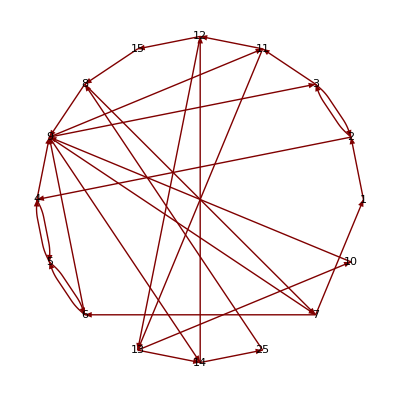
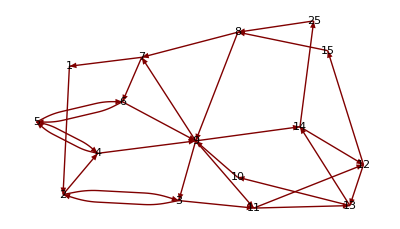
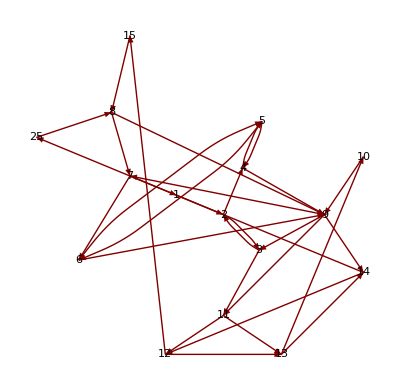
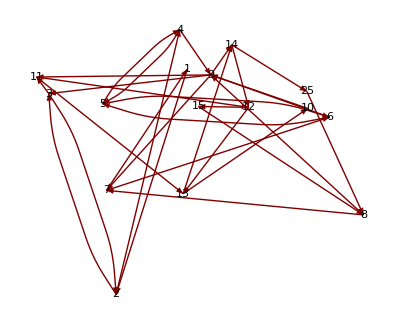
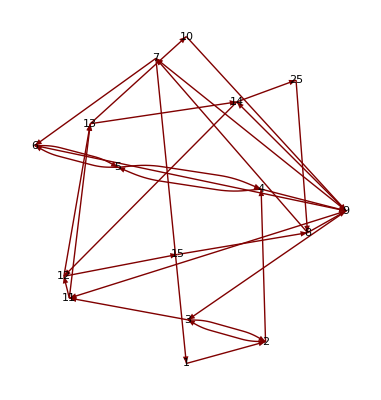
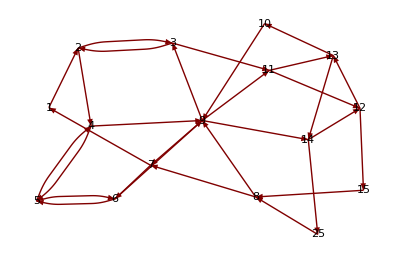
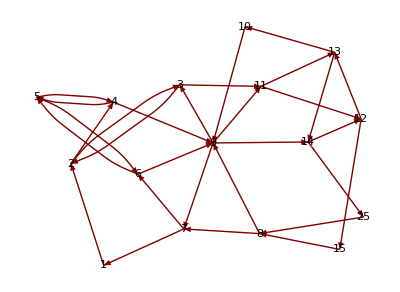

```mathematica
{{GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"CircularEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"HighDimensionalEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"RadialDrawing"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"RandomEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"SpiralEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"SpringElectricalEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"SpringEmbedding"]}}
```

```mathematica
{{GraphPlot3D[g,VertexLabeling->True]}, {GraphPlot3D[g,VertexLabeling->True,Method->"SpringEmbedding"]
GraphPlot3D[g,VertexLabeling->True,Method->"HighDimensionalEmbedding"]}}
```

{{-Graphics3D-},{-Graphics3D- -Graphics3D-}}

```mathematica
{{},},{},{-Graphics3D-},{-Graphics3D-},{},{-Graphics3D-}}
```

```mathematica
Bicomponents[g]
```

{{7,16},{5,4,6,7,8,13,10,14,25,11,12,15,9,3,2},{1,2}}

```mathematica
ClosenessCentrality[g]
```

{0.0166667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
cs=CommunityStructureAssignment[g]
Thread[Rule[VertexList[g],cs]]
```

{1,1,1,2,2,2,3,3,4,4,4,2,2,3,3,2,3}

{1→1,2→1,3→1,11→2,12→2,15→2,8→3,9→3,4→4,5→4,6→4,13→2,14→2,25→3,7→3,10→2,16→3}

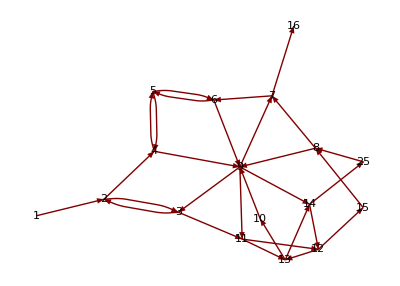

```mathematica
GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({Text[Framed[#2,Background->Hue[cs[[#3]]/4],FrameStyle->RGBColor[0.94,0.85,0.36]],#1]}&)]
```

```mathematica
EdgeList[g]
```

{{1,2},{2,3},{2,4},{3,11},{3,2},{11,12},{11,13},{12,15},{12,13},{15,8},{8,9},{8,7},{9,3},{9,11},{9,14},{9,7},{4,5},{4,9},{5,6},{5,4},{6,9},{6,5},{13,14},{13,10},{14,25},{14,12},{25,8},{7,6},{7,16},{10,9}}

{3→2,15→8,8→7,9→3,9→7,5→4,6→5,13→10,14→12,25→8,7→6,10→9}

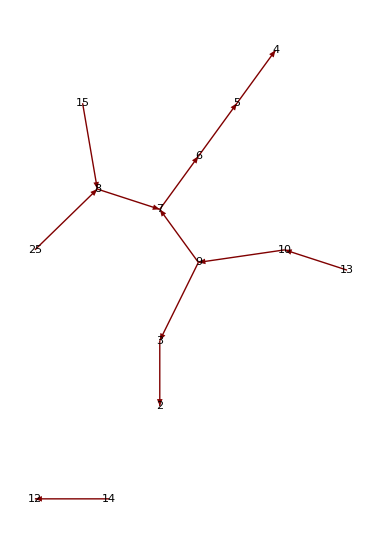

```mathematica
g2=Flatten[Map[If[#[[1]]>#[[2]],Rule@@#,{}]&,EdgeList[g]]]
GraphPlot[g2,DirectedEdges->True, VertexLabeling->True]
```

```mathematica
GraphCoordinates[g]
```

{{0.,0.661616},{1.00935,0.909275},{2.1224,0.713977},{3.07633,0.311599},{4.21664,0.158202},{4.88728,0.783611},{4.17285,1.67387},{3.04235,1.3938},{1.76126,1.62765},{1.7411,2.5258},{2.65281,2.39615},{3.72086,0.},{4.08466,0.832784},{4.89112,1.46951},{3.52249,2.45927},{3.34627,0.615707},{3.84825,3.50405}}

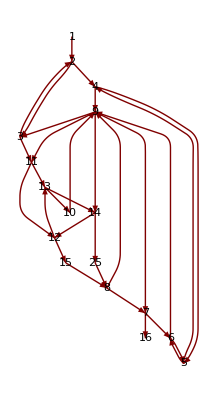

```mathematica
LayeredGraphPlot[g,VertexLabeling->True]
```

```mathematica
GraphDistanceMatrix[g]//MatrixForm
```

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 3 | 2 | 3 | 4 | 4 | 4 | 5 | 4 | 5 | 5
∞ | 0 | 1 | 2 | 3 | 4 | 5 | 2 | 1 | 2 | 3 | 3 | 3 | 4 | 3 | 4 | 4
∞ | 1 | 0 | 1 | 2 | 3 | 4 | 3 | 2 | 3 | 4 | 2 | 3 | 4 | 4 | 3 | 5
∞ | 5 | 4 | 0 | 1 | 2 | 3 | 3 | 6 | 6 | 5 | 1 | 2 | 3 | 4 | 2 | 5
∞ | 5 | 4 | 4 | 0 | 1 | 2 | 3 | 6 | 5 | 4 | 1 | 2 | 3 | 3 | 2 | 4
∞ | 4 | 3 | 3 | 4 | 0 | 1 | 2 | 5 | 4 | 3 | 4 | 3 | 4 | 2 | 5 | 3
∞ | 3 | 2 | 2 | 3 | 4 | 0 | 1 | 4 | 3 | 2 | 3 | 2 | 3 | 1 | 4 | 2
∞ | 2 | 1 | 1 | 2 | 3 | 3 | 0 | 3 | 3 | 2 | 2 | 1 | 2 | 1 | 3 | 2
∞ | 3 | 2 | 2 | 3 | 4 | 4 | 1 | 0 | 1 | 2 | 3 | 2 | 3 | 2 | 4 | 3
∞ | 4 | 3 | 3 | 4 | 5 | 5 | 2 | 1 | 0 | 1 | 4 | 3 | 4 | 3 | 5 | 4
∞ | 3 | 2 | 2 | 3 | 4 | 4 | 1 | 2 | 1 | 0 | 3 | 2 | 3 | 2 | 4 | 3
∞ | 4 | 3 | 3 | 2 | 3 | 3 | 2 | 5 | 5 | 4 | 0 | 1 | 2 | 3 | 1 | 4
∞ | 5 | 4 | 4 | 1 | 2 | 2 | 3 | 6 | 5 | 4 | 2 | 0 | 1 | 3 | 3 | 4
∞ | 4 | 3 | 3 | 4 | 5 | 1 | 2 | 5 | 4 | 3 | 4 | 3 | 0 | 2 | 5 | 3
∞ | 4 | 3 | 3 | 4 | 5 | 5 | 2 | 3 | 2 | 1 | 4 | 3 | 4 | 0 | 5 | 1
∞ | 3 | 2 | 2 | 3 | 4 | 4 | 1 | 4 | 4 | 3 | 3 | 2 | 3 | 2 | 0 | 3
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0)

```mathematica
HamiltonianCycles[g,All]
```

{}

```mathematica
MaximalBipartiteMatching[g]
```

{{1,2},{2,3},{3,11},{11,12},{12,15},{15,8},{6,9},{4,5},{5,6},{9,14},{14,25},{8,7},{13,10},{7,16}}

```mathematica
match=MaximalIndependentEdgeSet[g]
```

{{1,2},{3,9},{11,12},{15,8},{4,5},{6,7},{13,14}}

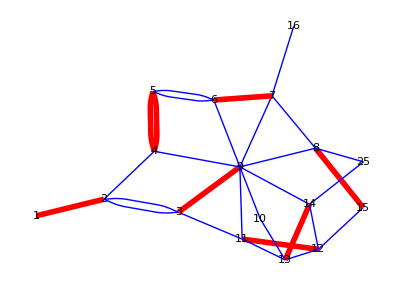

```mathematica
GraphPlot[g,DirectedEdges->True,EdgeRenderingFunction->({If[MemberQ[match,#2]||MemberQ[match,Reverse[#2]],{Red,Thickness[0.01],Line[#]},{Blue,Line[#]}]}&),VertexLabeling->True]
```

{1,3,12,8,4,6,10,16}

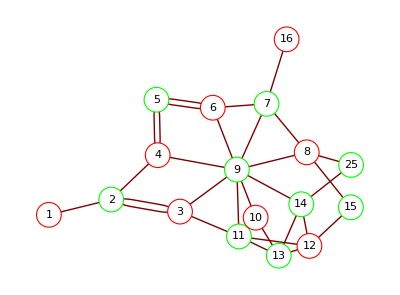

```mathematica
m=MaximalIndependentVertexSet[g]
GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({EdgeForm[If[MemberQ[m,#2],Red,Green]],White,Disk[#1,.2],Black,Text[#2,#1]}&)]
```

{{1,2,3,4,5,6,7,16},{11,12,15,8,9,13,14,25,10}}

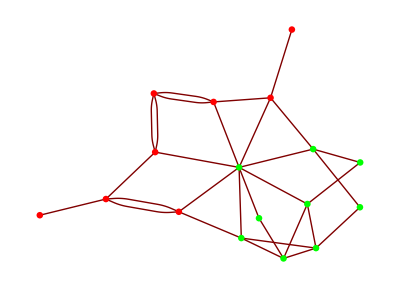

{{1,2,4,5,6},{3,11,9,13,14,10},{12,15,8,25,7,16}}

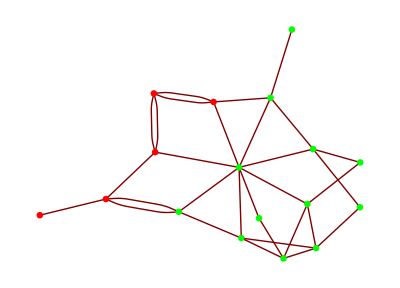

```mathematica
c=MinCut[g,2]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
c=MinCut[g,3]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
```

```mathematica
ls={1,2,3,41,17,29,28,39,23,24,33,32,13,38,40,41,3,4,5,6,7,8,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,10,8,7,25,13,27,19,28,29,18,30,31,13,42,21,35,20,27,31,14,37,38,39,5,43,6,25,12,44,32,45,42,27,30,15,36,40,39,4,2,43,7,11,46,33,45,22,39,35,19,30,16,36,37,13,44,46,25,47}
```

{1,2,3,41,17,29,28,39,23,24,33,32,13,38,40,41,3,4,5,6,7,8,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,10,8,7,25,13,27,19,28,29,18,30,31,13,42,21,35,20,27,31,14,37,38,39,5,43,6,25,12,44,32,45,42,27,30,15,36,40,39,4,2,43,7,11,46,33,45,22,39,35,19,30,16,36,37,13,44,46,25,47}

```mathematica
Length[ls]
```

97

```mathematica
Table[StringJoin[ToString[ls[[i]]],"->",ToString[ls[[i+1]]]],{i,1,Length[ls]-1}]
g=Map[ToExpression,%]
```

{1->2,2->3,3->41,41->17,17->29,29->28,28->39,39->23,23->24,24->33,33->32,32->13,13->38,38->40,40->41,41->3,3->4,4->5,5->6,6->7,7->8,8->10,10->11,11->12,12->13,13->14,14->15,15->16,16->17,17->18,18->19,19->20,20->21,21->22,22->23,23->24,24->25,25->10,10->8,8->7,7->25,25->13,13->27,27->19,19->28,28->29,29->18,18->30,30->31,31->13,13->42,42->21,21->35,35->20,20->27,27->31,31->14,14->37,37->38,38->39,39->5,5->43,43->6,6->25,25->12,12->44,44->32,32->45,45->42,42->27,27->30,30->15,15->36,36->40,40->39,39->4,4->2,2->43,43->7,7->11,11->46,46->33,33->45,45->22,22->39,39->35,35->19,19->30,30->16,16->36,36->37,37->13,13->44,44->46,46->25,25->47}

{1→2,2→3,3→41,41→17,17→29,29→28,28→39,39→23,23→24,24→33,33→32,32→13,13→38,38→40,40→41,41→3,3→4,4→5,5→6,6→7,7→8,8→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20,20→21,21→22,22→23,23→24,24→25,25→10,10→8,8→7,7→25,25→13,13→27,27→19,19→28,28→29,29→18,18→30,30→31,31→13,13→42,42→21,21→35,35→20,20→27,27→31,31→14,14→37,37→38,38→39,39→5,5→43,43→6,6→25,25→12,12→44,44→32,32→45,45→42,42→27,27→30,30→15,15→36,36→40,40→39,39→4,4→2,2→43,43→7,7→11,11→46,46→33,33→45,45→22,22→39,39→35,35→19,19→30,30→16,16→36,36→37,37→13,13→44,44→46,46→25,25→47}

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

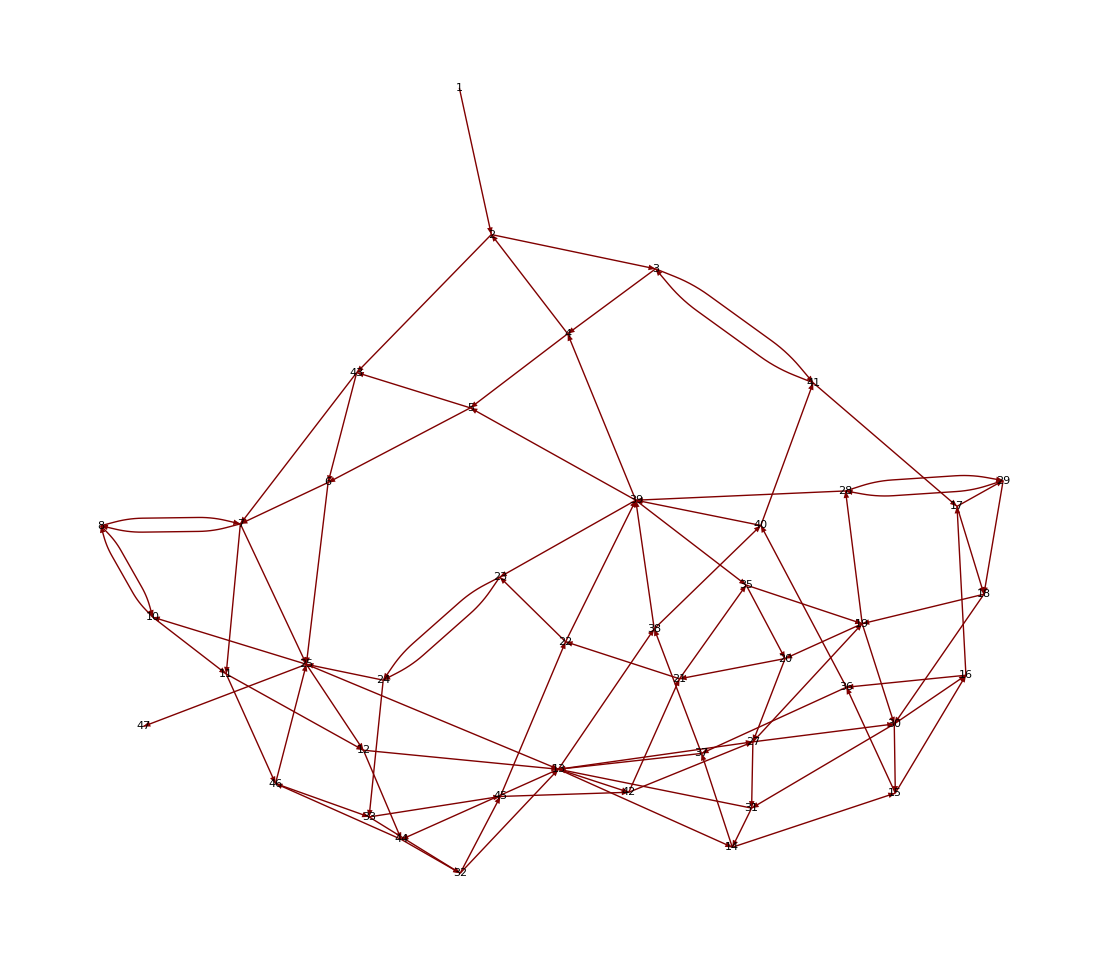

GraphPlot::grph: gg is not a valid graph.

GraphPlot[gg,DirectedEdges→True,VertexLabeling→True]

{{25,47},{12,44,11,46,25,10,8,7,43,6,5,39,37,36,14,45,22,42,21,35,19,18,30,20,27,31,15,16,17,29,28,23,24,33,32,13,38,40,41,3,4,2},{1,2}}

{0.00420168,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1,1,1,1,2,3,3,1,4,4,4,4,5,1,1,1,6,6,6,6,6,6,6,2,2,2,5,5,5,5,4,6,5,5,5,5,5,2,6,6,4,2,6,6}

{1→1,2→1,3→1,41→1,17→2,29→3,28→3,39→1,23→4,24→4,33→4,32→4,13→5,38→1,40→1,4→1,5→6,6→6,7→6,8→6,10→6,11→6,12→6,14→2,15→2,16→2,18→5,19→5,20→5,21→5,22→4,25→6,27→5,30→5,31→5,42→5,35→5,37→2,43→6,44→6,45→4,36→2,46→6,47→6}

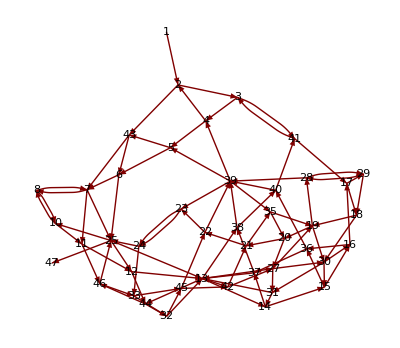

{{1,2},{2,3},{2,43},{3,41},{3,4},{41,17},{41,3},{17,29},{17,18},{29,28},{29,18},{28,39},{28,29},{39,23},{39,5},{39,4},{39,35},{23,24},{24,33},{24,25},{33,32},{33,45},{32,13},{32,45},{13,38},{13,14},{13,27},{13,42},{13,44},{38,40},{38,39},{40,41},{40,39},{4,5},{4,2},{5,6},{5,43},{6,7},{6,25},{7,8},{7,25},{7,11},{8,10},{8,7},{10,11},{10,8},{11,12},{11,46},{12,13},{12,44},{14,15},{14,37},{15,16},{15,36},{16,17},{16,36},{18,19},{18,30},{19,20},{19,28},{19,30},{20,21},{20,27},{21,22},{21,35},{22,23},{22,39},{25,10},{25,13},{25,12},{25,47},{27,19},{27,31},{27,30},{30,31},{30,15},{30,16},{31,13},{31,14},{42,21},{42,27},{35,20},{35,19},{37,38},{37,13},{43,6},{43,7},{44,32},{44,46},{45,42},{45,22},{36,40},{36,37},{46,33},{46,25}}

{41→17,41→3,29→28,29→18,39→23,39→5,39→4,39→35,33→32,32→13,40→39,4→2,8→7,10→8,25→10,25→13,25→12,27→19,30→15,30→16,31→13,31→14,42→21,42→27,35→20,35→19,37→13,43→6,43→7,44→32,45→42,45→22,46→33,46→25}

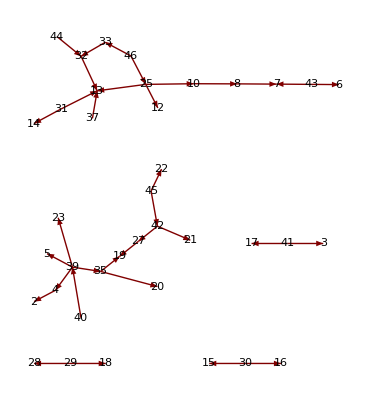

{{2.52827,5.54063},{2.75419,4.50555},{3.91236,4.26335},{5.0245,3.45948},{6.03892,2.58794},{6.3643,2.77002},{5.25259,2.69668},{3.77296,2.63127},{2.81367,2.08918},{1.99154,1.36193},{1.89224,0.397054},{2.5347,0.},{3.22734,0.733402},{3.90328,1.72388},{4.65527,2.45339},{3.29259,3.80538},{2.60611,3.28266},{1.60296,2.75649},{0.984062,2.46427},{0.,2.45141},{0.365995,1.80637},{0.884116,1.40596},{1.85188,0.867717},{4.45389,0.183155},{5.60369,0.565117},{6.10173,1.39664},{6.22888,1.96825},{5.37014,1.76028},{4.82635,1.51427},{4.08153,1.37138},{3.27799,1.63288},{1.4496,1.47381},{4.59913,0.926718},{5.59627,1.05293},{4.59014,0.459297},{3.72355,0.571065},{4.55185,2.03269},{4.23673,0.844985},{1.80467,3.53178},{2.11956,0.238151},{2.81769,0.541519},{5.25871,1.31205},{1.23188,0.632865},{0.299519,1.03542}}

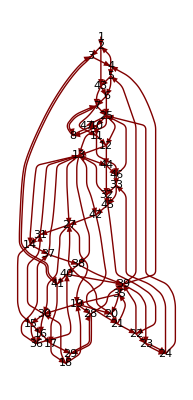

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 10 | 6 | 7 | 5 | 6 | 7 | 3 | 4 | 3 | 3 | 4 | 5 | 4 | 5 | 6 | 7 | 7 | 5 | 6 | 7 | 7 | 8 | 4 | 6 | 6 | 7 | 6 | 8 | 7 | 2 | 6 | 7 | 8 | 5 | 5
∞ | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 9 | 5 | 6 | 4 | 5 | 6 | 2 | 3 | 2 | 2 | 3 | 4 | 3 | 4 | 5 | 6 | 6 | 4 | 5 | 6 | 6 | 7 | 3 | 5 | 5 | 6 | 5 | 7 | 6 | 1 | 5 | 6 | 7 | 4 | 4
∞ | 2 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 8 | 7 | 7 | 5 | 6 | 7 | 1 | 2 | 3 | 4 | 5 | 5 | 5 | 5 | 6 | 5 | 5 | 3 | 4 | 5 | 6 | 7 | 4 | 6 | 4 | 5 | 6 | 6 | 7 | 3 | 6 | 8 | 6 | 6 | 5
∞ | 3 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 7 | 8 | 7 | 5 | 6 | 6 | 2 | 3 | 4 | 5 | 6 | 6 | 6 | 6 | 5 | 4 | 4 | 2 | 3 | 4 | 5 | 6 | 5 | 5 | 3 | 4 | 6 | 5 | 6 | 4 | 6 | 8 | 5 | 7 | 6
∞ | 5 | 6 | 6 | 0 | 1 | 2 | 3 | 4 | 6 | 7 | 6 | 4 | 5 | 5 | 4 | 4 | 5 | 6 | 7 | 7 | 7 | 7 | 4 | 3 | 3 | 1 | 2 | 3 | 4 | 5 | 6 | 4 | 2 | 3 | 5 | 4 | 5 | 5 | 5 | 7 | 4 | 6 | 7
∞ | 4 | 5 | 6 | 4 | 0 | 1 | 2 | 3 | 5 | 6 | 6 | 4 | 5 | 5 | 3 | 3 | 4 | 5 | 6 | 6 | 6 | 6 | 4 | 3 | 3 | 1 | 2 | 3 | 4 | 5 | 5 | 4 | 2 | 3 | 5 | 3 | 5 | 4 | 5 | 7 | 4 | 6 | 6
∞ | 3 | 4 | 5 | 5 | 1 | 0 | 1 | 2 | 4 | 5 | 6 | 5 | 6 | 6 | 2 | 2 | 3 | 4 | 5 | 5 | 5 | 5 | 5 | 4 | 4 | 2 | 3 | 3 | 4 | 5 | 4 | 4 | 3 | 4 | 6 | 2 | 6 | 3 | 6 | 6 | 5 | 6 | 5
∞ | 2 | 3 | 4 | 5 | 4 | 3 | 0 | 1 | 3 | 4 | 5 | 4 | 5 | 6 | 1 | 1 | 2 | 3 | 4 | 4 | 4 | 4 | 5 | 4 | 4 | 5 | 2 | 2 | 3 | 4 | 3 | 3 | 3 | 4 | 5 | 1 | 6 | 2 | 5 | 5 | 5 | 5 | 4
∞ | 8 | 8 | 7 | 8 | 8 | 7 | 6 | 0 | 2 | 3 | 4 | 4 | 5 | 6 | 7 | 7 | 8 | 6 | 5 | 4 | 5 | 4 | 5 | 6 | 7 | 9 | 6 | 7 | 6 | 5 | 3 | 5 | 6 | 6 | 5 | 7 | 6 | 8 | 5 | 4 | 7 | 6 | 4
∞ | 6 | 6 | 5 | 6 | 6 | 5 | 4 | 4 | 0 | 1 | 2 | 2 | 3 | 4 | 5 | 5 | 6 | 4 | 3 | 2 | 3 | 2 | 3 | 4 | 5 | 7 | 4 | 5 | 4 | 3 | 1 | 3 | 4 | 4 | 3 | 5 | 4 | 6 | 3 | 2 | 5 | 4 | 2
∞ | 5 | 6 | 5 | 6 | 6 | 5 | 3 | 3 | 5 | 0 | 1 | 2 | 3 | 4 | 4 | 4 | 5 | 6 | 7 | 6 | 7 | 6 | 3 | 4 | 5 | 7 | 4 | 5 | 3 | 2 | 5 | 3 | 4 | 4 | 2 | 4 | 4 | 5 | 3 | 1 | 5 | 4 | 6
∞ | 5 | 5 | 4 | 5 | 5 | 4 | 3 | 3 | 5 | 4 | 0 | 1 | 2 | 3 | 4 | 4 | 5 | 6 | 6 | 5 | 6 | 5 | 2 | 3 | 4 | 6 | 3 | 4 | 3 | 2 | 4 | 2 | 3 | 3 | 2 | 4 | 3 | 5 | 2 | 1 | 4 | 3 | 5
∞ | 4 | 4 | 3 | 4 | 4 | 3 | 2 | 3 | 5 | 3 | 2 | 0 | 1 | 2 | 3 | 3 | 4 | 5 | 5 | 4 | 5 | 4 | 1 | 2 | 3 | 5 | 2 | 3 | 2 | 3 | 3 | 1 | 2 | 2 | 1 | 3 | 2 | 4 | 1 | 3 | 3 | 2 | 4
∞ | 3 | 3 | 2 | 3 | 4 | 4 | 1 | 2 | 4 | 5 | 6 | 5 | 0 | 1 | 2 | 2 | 3 | 4 | 5 | 5 | 5 | 5 | 6 | 5 | 5 | 4 | 3 | 3 | 4 | 5 | 4 | 4 | 4 | 5 | 6 | 2 | 7 | 3 | 6 | 6 | 6 | 6 | 5
∞ | 3 | 2 | 1 | 2 | 3 | 4 | 1 | 2 | 4 | 5 | 6 | 5 | 6 | 0 | 2 | 2 | 3 | 4 | 5 | 5 | 5 | 5 | 6 | 5 | 5 | 3 | 3 | 3 | 4 | 5 | 4 | 4 | 4 | 5 | 6 | 2 | 7 | 3 | 6 | 6 | 6 | 6 | 5
∞ | 1 | 2 | 3 | 4 | 5 | 6 | 6 | 7 | 9 | 6 | 6 | 4 | 5 | 6 | 0 | 1 | 2 | 3 | 4 | 4 | 4 | 4 | 5 | 6 | 7 | 5 | 6 | 7 | 6 | 7 | 3 | 5 | 6 | 6 | 5 | 7 | 6 | 2 | 5 | 7 | 7 | 5 | 4
∞ | 7 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 8 | 5 | 5 | 3 | 4 | 5 | 6 | 0 | 1 | 2 | 3 | 3 | 3 | 3 | 4 | 5 | 6 | 8 | 5 | 6 | 5 | 6 | 2 | 4 | 5 | 5 | 4 | 6 | 5 | 1 | 4 | 6 | 6 | 4 | 3
∞ | 6 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 7 | 4 | 4 | 2 | 3 | 4 | 5 | 5 | 0 | 1 | 2 | 2 | 2 | 2 | 3 | 4 | 5 | 7 | 4 | 5 | 4 | 5 | 1 | 3 | 4 | 4 | 3 | 5 | 4 | 6 | 3 | 5 | 5 | 3 | 2
∞ | 6 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 7 | 3 | 4 | 2 | 3 | 4 | 5 | 5 | 6 | 0 | 1 | 2 | 1 | 2 | 3 | 4 | 5 | 7 | 4 | 5 | 4 | 5 | 1 | 3 | 4 | 4 | 3 | 5 | 4 | 6 | 3 | 4 | 5 | 2 | 2
∞ | 7 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 8 | 4 | 5 | 3 | 4 | 5 | 6 | 6 | 7 | 1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 8 | 5 | 6 | 5 | 6 | 2 | 4 | 5 | 5 | 4 | 6 | 5 | 7 | 4 | 5 | 6 | 3 | 3
∞ | 7 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 8 | 3 | 4 | 3 | 4 | 5 | 6 | 6 | 7 | 2 | 1 | 0 | 1 | 2 | 4 | 5 | 6 | 8 | 5 | 6 | 5 | 5 | 3 | 4 | 5 | 5 | 4 | 6 | 5 | 7 | 3 | 4 | 6 | 2 | 4
∞ | 6 | 6 | 5 | 6 | 6 | 5 | 4 | 5 | 7 | 2 | 3 | 2 | 3 | 4 | 5 | 5 | 6 | 5 | 4 | 3 | 0 | 1 | 3 | 4 | 5 | 7 | 4 | 5 | 4 | 4 | 2 | 3 | 4 | 4 | 3 | 5 | 4 | 6 | 2 | 3 | 5 | 1 | 3
∞ | 5 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 6 | 3 | 2 | 1 | 2 | 3 | 4 | 4 | 5 | 6 | 5 | 4 | 5 | 0 | 2 | 3 | 4 | 6 | 3 | 4 | 3 | 4 | 3 | 2 | 3 | 3 | 2 | 4 | 3 | 5 | 1 | 3 | 4 | 2 | 4
∞ | 5 | 5 | 4 | 3 | 4 | 5 | 3 | 4 | 6 | 5 | 4 | 2 | 2 | 3 | 4 | 4 | 5 | 6 | 7 | 6 | 7 | 6 | 0 | 1 | 2 | 4 | 4 | 5 | 4 | 5 | 5 | 3 | 4 | 4 | 3 | 4 | 1 | 5 | 3 | 5 | 2 | 4 | 6
∞ | 5 | 4 | 3 | 2 | 3 | 4 | 3 | 4 | 6 | 6 | 5 | 3 | 3 | 2 | 4 | 4 | 5 | 6 | 7 | 7 | 7 | 7 | 4 | 0 | 1 | 3 | 4 | 5 | 5 | 6 | 6 | 4 | 4 | 5 | 4 | 4 | 2 | 5 | 4 | 6 | 1 | 5 | 7
∞ | 5 | 4 | 3 | 1 | 2 | 3 | 3 | 4 | 6 | 6 | 5 | 3 | 3 | 2 | 4 | 4 | 5 | 6 | 7 | 7 | 7 | 7 | 4 | 4 | 0 | 2 | 3 | 4 | 5 | 6 | 6 | 4 | 3 | 4 | 4 | 4 | 2 | 5 | 4 | 6 | 1 | 5 | 7
∞ | 5 | 6 | 5 | 3 | 3 | 2 | 3 | 4 | 6 | 6 | 5 | 3 | 4 | 4 | 4 | 4 | 5 | 6 | 7 | 7 | 7 | 7 | 3 | 2 | 2 | 0 | 1 | 2 | 3 | 4 | 6 | 3 | 1 | 2 | 4 | 4 | 4 | 5 | 4 | 6 | 3 | 5 | 7
∞ | 4 | 5 | 5 | 3 | 2 | 1 | 2 | 3 | 5 | 6 | 5 | 3 | 4 | 4 | 3 | 3 | 4 | 5 | 6 | 6 | 6 | 6 | 3 | 2 | 2 | 3 | 0 | 1 | 2 | 3 | 5 | 2 | 1 | 2 | 4 | 3 | 4 | 4 | 4 | 6 | 3 | 5 | 6
∞ | 5 | 6 | 6 | 4 | 4 | 3 | 3 | 3 | 5 | 6 | 5 | 3 | 4 | 5 | 4 | 4 | 5 | 6 | 7 | 7 | 7 | 7 | 3 | 3 | 3 | 5 | 2 | 0 | 1 | 2 | 6 | 1 | 2 | 2 | 4 | 2 | 4 | 5 | 4 | 6 | 4 | 5 | 7
∞ | 4 | 5 | 6 | 5 | 4 | 3 | 2 | 2 | 4 | 5 | 6 | 5 | 6 | 6 | 3 | 3 | 4 | 5 | 6 | 6 | 6 | 6 | 5 | 4 | 4 | 5 | 2 | 2 | 0 | 1 | 5 | 3 | 3 | 4 | 6 | 1 | 6 | 4 | 6 | 6 | 5 | 7 | 6
∞ | 3 | 4 | 5 | 6 | 5 | 4 | 1 | 1 | 3 | 4 | 5 | 5 | 6 | 7 | 2 | 2 | 3 | 4 | 5 | 5 | 5 | 5 | 6 | 5 | 5 | 6 | 3 | 3 | 4 | 0 | 4 | 4 | 4 | 5 | 6 | 2 | 7 | 3 | 6 | 5 | 6 | 6 | 5
∞ | 5 | 5 | 4 | 5 | 5 | 4 | 3 | 4 | 6 | 4 | 3 | 1 | 2 | 3 | 4 | 4 | 5 | 3 | 2 | 1 | 2 | 1 | 2 | 3 | 4 | 6 | 3 | 4 | 3 | 4 | 0 | 2 | 3 | 3 | 2 | 4 | 3 | 5 | 2 | 4 | 4 | 3 | 1
∞ | 5 | 6 | 5 | 3 | 3 | 2 | 3 | 4 | 6 | 5 | 4 | 2 | 3 | 4 | 4 | 4 | 5 | 6 | 7 | 6 | 7 | 6 | 2 | 2 | 2 | 4 | 1 | 2 | 3 | 4 | 5 | 0 | 1 | 1 | 3 | 4 | 3 | 5 | 3 | 5 | 3 | 4 | 6
∞ | 6 | 5 | 4 | 2 | 3 | 4 | 4 | 5 | 7 | 5 | 4 | 2 | 3 | 3 | 5 | 5 | 6 | 7 | 7 | 6 | 7 | 6 | 2 | 1 | 1 | 3 | 4 | 5 | 4 | 5 | 5 | 3 | 0 | 1 | 3 | 5 | 3 | 6 | 3 | 5 | 2 | 4 | 6
∞ | 5 | 5 | 4 | 4 | 5 | 4 | 3 | 4 | 6 | 4 | 3 | 1 | 2 | 3 | 4 | 4 | 5 | 6 | 6 | 5 | 6 | 5 | 1 | 2 | 3 | 5 | 3 | 4 | 3 | 4 | 4 | 2 | 3 | 0 | 2 | 4 | 2 | 5 | 2 | 4 | 3 | 3 | 5
∞ | 5 | 6 | 6 | 4 | 4 | 3 | 3 | 3 | 5 | 6 | 5 | 3 | 4 | 5 | 4 | 4 | 5 | 6 | 7 | 7 | 7 | 7 | 3 | 3 | 3 | 5 | 2 | 3 | 1 | 2 | 6 | 1 | 2 | 2 | 0 | 2 | 4 | 5 | 4 | 6 | 4 | 5 | 7
∞ | 5 | 6 | 6 | 4 | 3 | 2 | 3 | 4 | 6 | 7 | 6 | 4 | 5 | 5 | 4 | 4 | 5 | 6 | 7 | 7 | 7 | 7 | 4 | 3 | 3 | 4 | 1 | 1 | 2 | 3 | 6 | 2 | 2 | 3 | 5 | 0 | 5 | 5 | 5 | 7 | 4 | 6 | 7
∞ | 4 | 4 | 3 | 4 | 5 | 4 | 2 | 3 | 5 | 4 | 3 | 1 | 1 | 2 | 3 | 3 | 4 | 5 | 6 | 5 | 6 | 5 | 2 | 3 | 4 | 5 | 3 | 4 | 3 | 4 | 4 | 2 | 3 | 3 | 2 | 3 | 0 | 4 | 2 | 4 | 4 | 3 | 5
∞ | 7 | 7 | 6 | 7 | 7 | 6 | 5 | 6 | 8 | 4 | 5 | 3 | 4 | 5 | 6 | 6 | 1 | 1 | 2 | 3 | 2 | 3 | 4 | 5 | 6 | 8 | 5 | 6 | 5 | 6 | 2 | 4 | 5 | 5 | 4 | 6 | 5 | 0 | 4 | 5 | 6 | 3 | 3
∞ | 6 | 6 | 5 | 6 | 6 | 5 | 4 | 4 | 6 | 2 | 1 | 2 | 3 | 4 | 5 | 5 | 6 | 5 | 4 | 3 | 4 | 3 | 3 | 4 | 5 | 7 | 4 | 5 | 4 | 3 | 2 | 3 | 4 | 4 | 3 | 5 | 4 | 6 | 0 | 2 | 5 | 1 | 3
∞ | 4 | 5 | 6 | 5 | 5 | 4 | 2 | 2 | 4 | 5 | 6 | 4 | 5 | 6 | 3 | 3 | 4 | 5 | 6 | 6 | 6 | 6 | 4 | 4 | 4 | 6 | 3 | 4 | 2 | 1 | 5 | 2 | 3 | 3 | 1 | 3 | 5 | 4 | 5 | 0 | 5 | 6 | 6
∞ | 4 | 3 | 2 | 3 | 4 | 5 | 2 | 3 | 5 | 5 | 4 | 2 | 2 | 1 | 3 | 3 | 4 | 5 | 6 | 6 | 6 | 6 | 3 | 4 | 5 | 4 | 4 | 4 | 4 | 5 | 5 | 3 | 4 | 4 | 3 | 3 | 1 | 4 | 3 | 5 | 0 | 4 | 6
∞ | 6 | 6 | 5 | 6 | 6 | 5 | 4 | 4 | 6 | 1 | 2 | 2 | 3 | 4 | 5 | 5 | 6 | 4 | 3 | 2 | 3 | 2 | 3 | 4 | 5 | 7 | 4 | 5 | 4 | 3 | 1 | 3 | 4 | 4 | 3 | 5 | 4 | 6 | 3 | 2 | 5 | 0 | 2
∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | ∞ | 0)

{}

{{1,2},{2,3},{40,41},{41,17},{17,29},{19,28},{28,39},{22,23},{23,24},{24,33},{33,32},{37,13},{13,38},{38,40},{3,4},{4,5},{43,6},{6,7},{7,8},{8,10},{10,11},{11,12},{31,14},{14,15},{15,16},{29,18},{18,19},{35,20},{20,21},{21,22},{46,25},{42,27},{27,30},{30,31},{45,42},{39,35},{36,37},{5,43},{12,44},{32,45},{16,36},{44,46},{25,47}}

{{1,2},{3,41},{17,16},{29,28},{39,38},{23,22},{24,33},{32,44},{13,12},{40,36},{4,5},{6,43},{7,8},{10,25},{11,46},{14,31},{15,30},{18,19},{20,35},{21,42}}

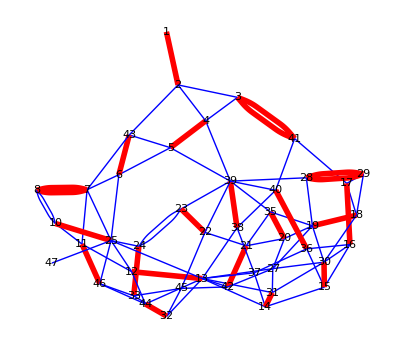

{1,3,17,28,23,33,13,40,5,7,10,15,20,47}

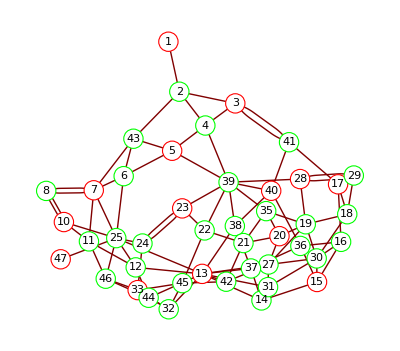

{{1,2,3,23,24,33,32,4,5,6,7,8,10,11,12,22,25,43,44,45,46,47},{41,17,29,28,39,13,38,40,14,15,16,18,19,20,21,27,30,31,42,35,37,36}}

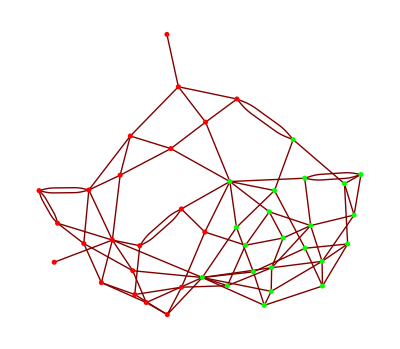

{{17,29,28,14,15,16,18,19,20,27,30,31,35,36},{24,33,32,13,7,8,10,11,12,25,42,44,45,46,47},{1,2,3,41,39,23,38,40,4,5,6,21,22,37,43}}

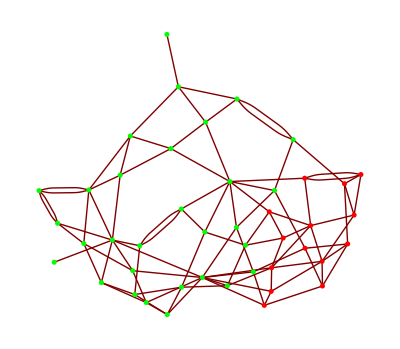

```mathematica
Needs["GraphUtilities`"];
AdjacencyMatrix[g]//MatrixForm
GraphPlot[g,DirectedEdges->True,VertexLabeling->True]
GraphPlot[gg,DirectedEdges->True,VertexLabeling->True]
Bicomponents[g]
ClosenessCentrality[g]
cs=CommunityStructureAssignment[g]
Thread[Rule[VertexList[g],cs]]
GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({Text[Framed[#2,Background->Hue[cs[[#3]]/4],FrameStyle->RGBColor[0.94,0.85,0.36]],#1]}&)]
EdgeList[g]
g2=Flatten[Map[If[#[[1]]>#[[2]],Rule@@#,{}]&,EdgeList[g]]]
GraphPlot[g2,DirectedEdges->True, VertexLabeling->True]
GraphCoordinates[g]
LayeredGraphPlot[g,VertexLabeling->True]
GraphDistanceMatrix[g]//MatrixForm
HamiltonianCycles[g,All]
MaximalBipartiteMatching[g]
match=MaximalIndependentEdgeSet[g]
GraphPlot[g,DirectedEdges->True,EdgeRenderingFunction->({If[MemberQ[match,#2]||MemberQ[match,Reverse[#2]],{Red,Thickness[0.01],Line[#]},{Blue,Line[#]}]}&),VertexLabeling->True]
m=MaximalIndependentVertexSet[g]
GraphPlot[g,DirectedEdges->True,VertexRenderingFunction->({EdgeForm[If[MemberQ[m,#2],Red,Green]],White,Disk[#1,.2],Black,Text[#2,#1]}&)]
c=MinCut[g,2]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
c=MinCut[g,3]
GraphPlot[g,VertexRenderingFunction->({If[MemberQ[c⟦1⟧,#2],Red,Green],Disk[#1,.05]}&)]
```

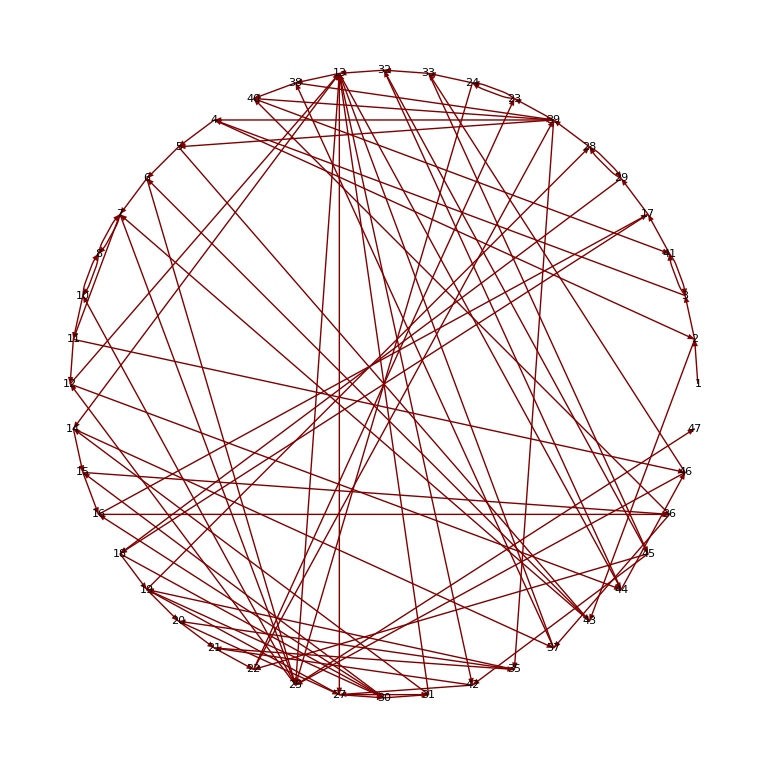
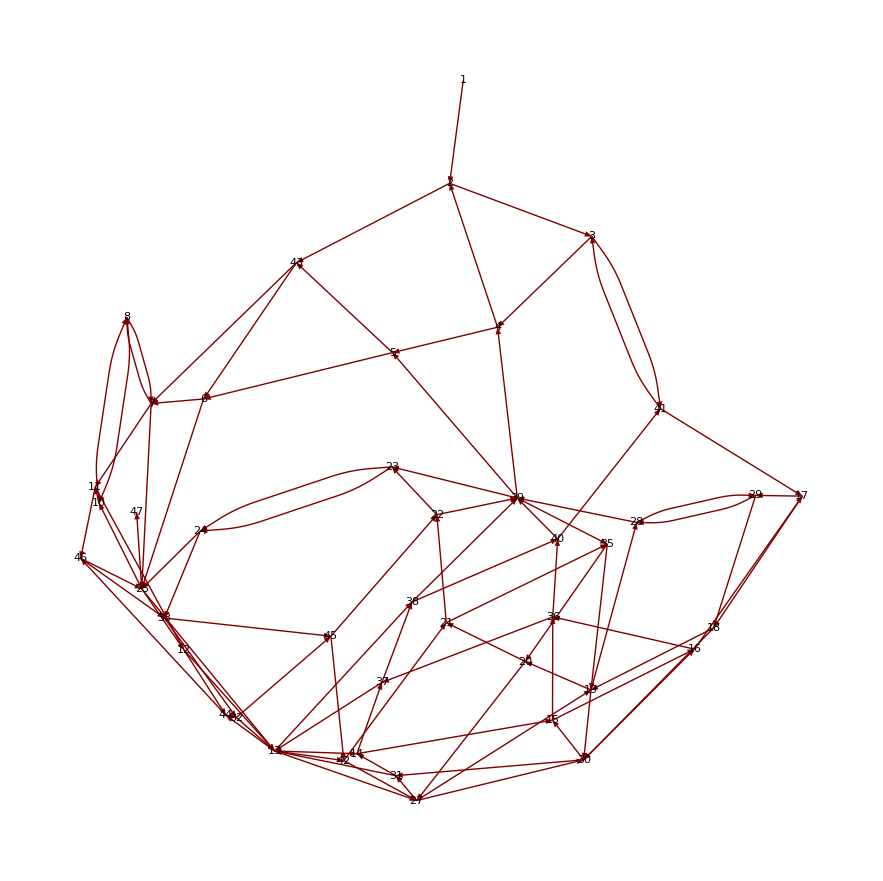
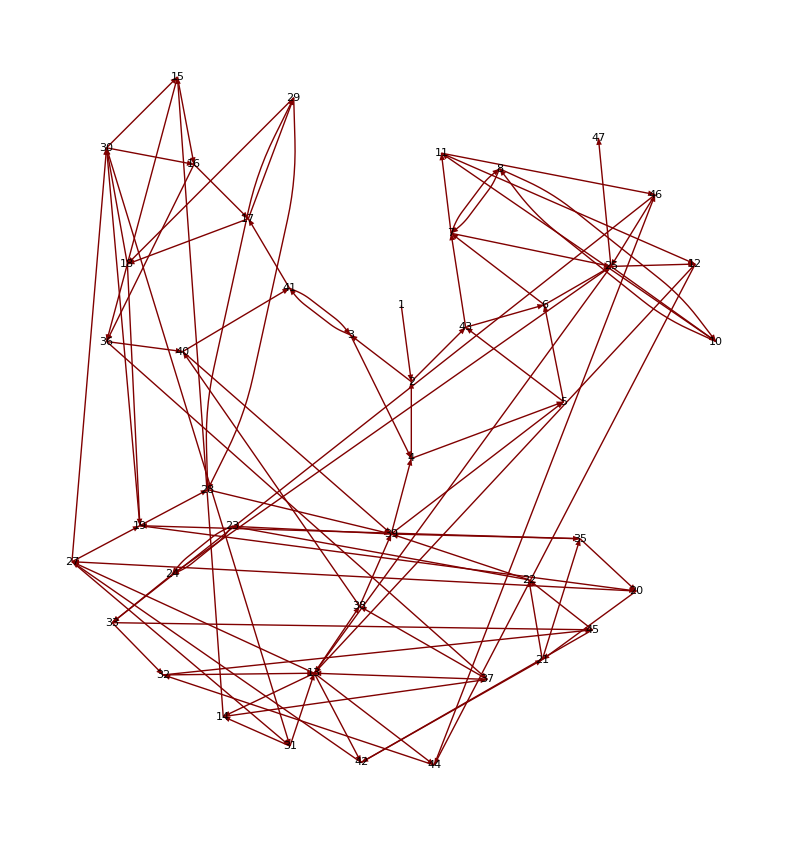
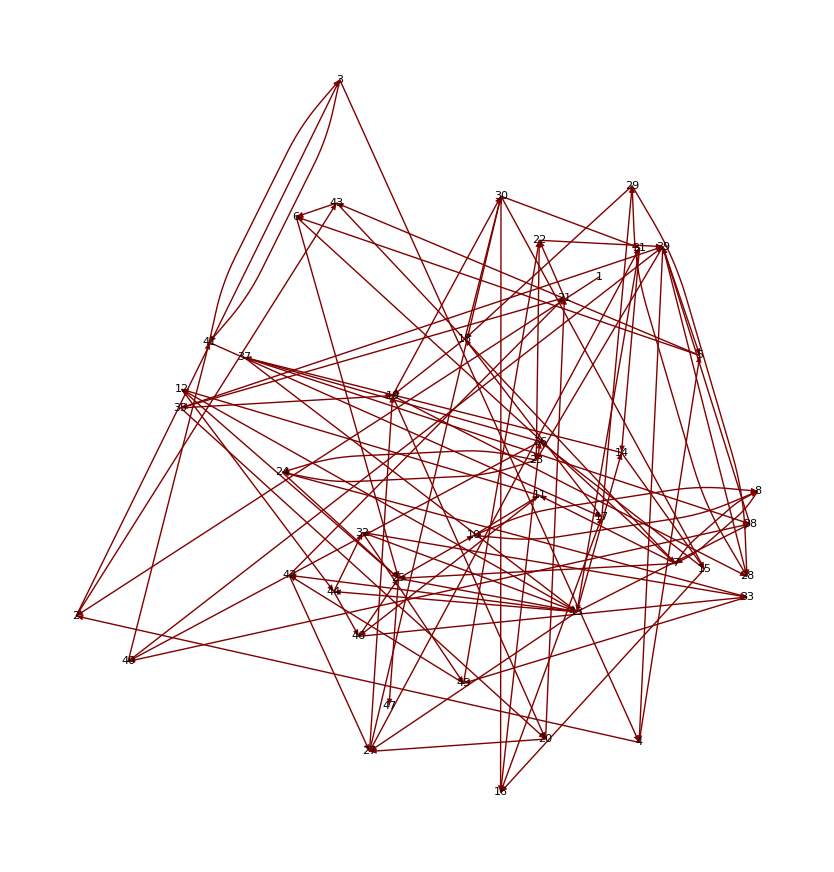
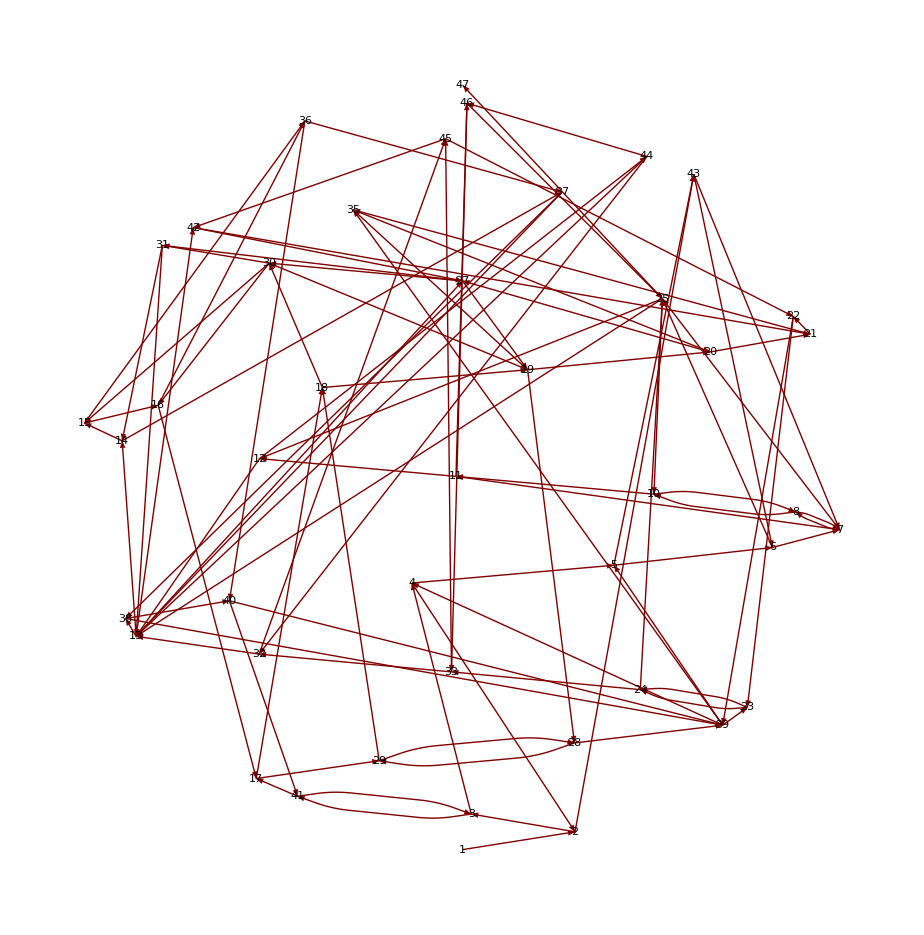
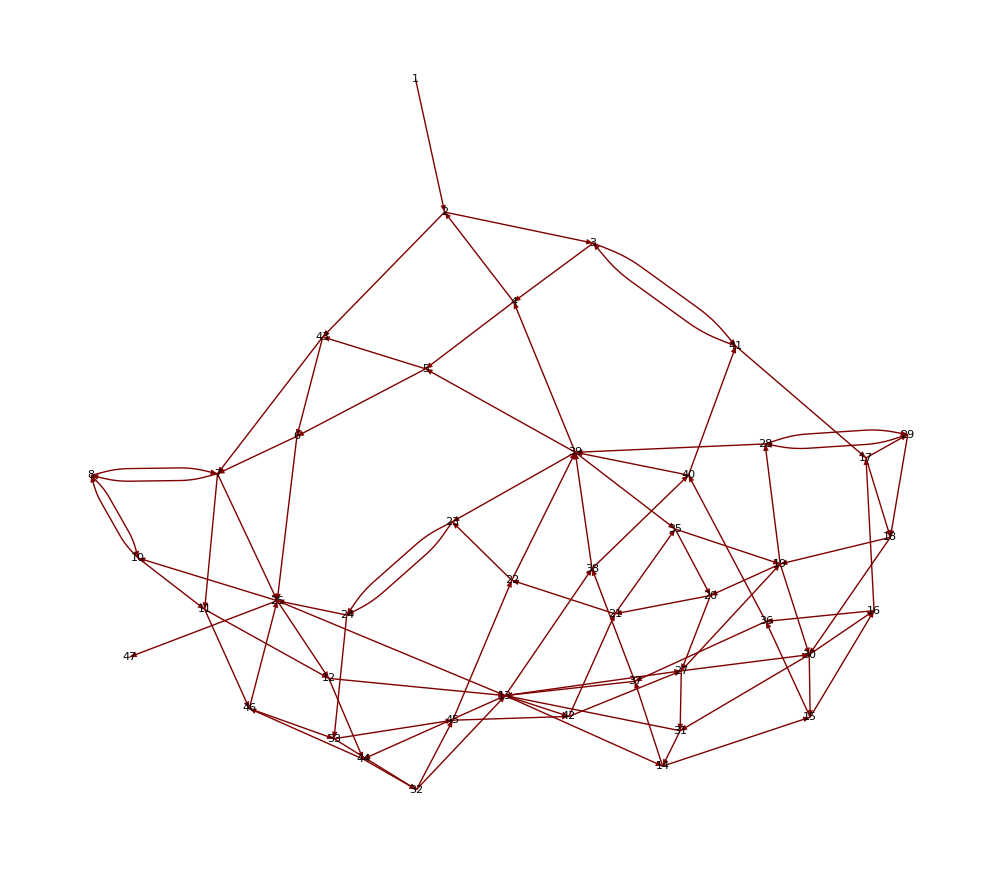
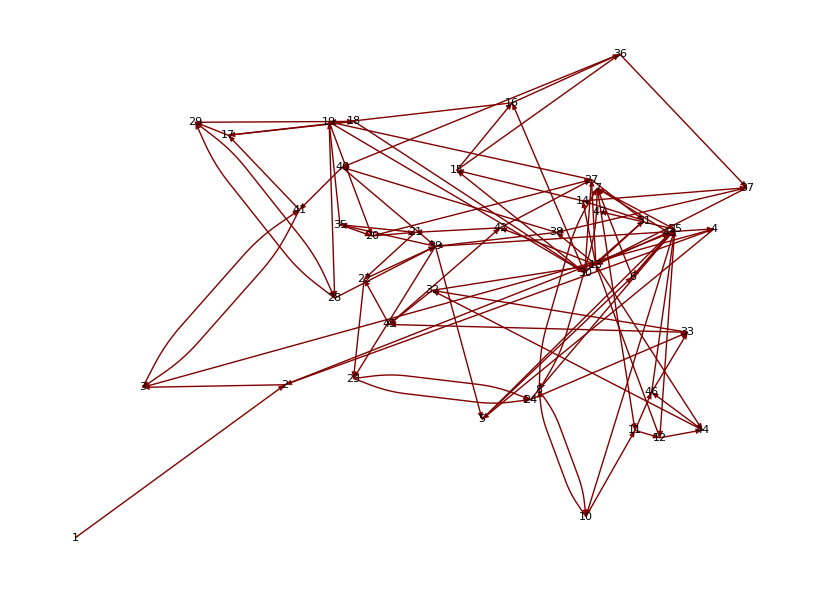

{{-Graphics3D-},{-Graphics3D- -Graphics3D-}}

```mathematica
{{GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"CircularEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"HighDimensionalEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"RadialDrawing"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"RandomEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"SpiralEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"SpringElectricalEmbedding"]}, {GraphPlot[g,DirectedEdges->True,VertexLabeling->True,Method->"SpringEmbedding"]}}
{{GraphPlot3D[g,VertexLabeling->True]}, {GraphPlot3D[g,VertexLabeling->True,Method->"SpringEmbedding"]
GraphPlot3D[g,VertexLabeling->True,Method->"HighDimensionalEmbedding"]}}
```

```mathematica
g
```

```mathematica
g={1->2,2->3,3->41,41->17,17->29,29->28,28->39,39->23,23->24,24->33,33->32,32->13,13->38,38->40,40->41,41->3,3->4,4->5,5->6,6->7,7->8,8->10,10->11,11->12,12->13,13->14,14->15,15->16,16->17,17->18,18->19,19->20,20->21,21->22,22->23,23->24,24->25,25->10,10->8,8->7,7->25,25->13,13->27,27->19,19->28,28->29,29->18,18->30,30->31,31->13,13->42,42->21,21->35,35->20,20->27,27->31,31->14,14->37,37->38,38->39,39->5,5->43,43->6,6->25,25->12,12->44,44->32,32->45,45->42,42->27,27->30,30->15,15->36,36->40,40->39,39->4,4->2,2->43,43->7,7->11,11->46,46->33,33->45,45->22,22->39,39->35,35->19,19->30,30->16,16->36,36->37,37->13,13->44,44->46,46->25,25->1}
```

{1→2,2→3,3→41,41→17,17→29,29→28,28→39,39→23,23→24,24→33,33→32,32→13,13→38,38→40,40→41,41→3,3→4,4→5,5→6,6→7,7→8,8→10,10→11,11→12,12→13,13→14,14→15,15→16,16→17,17→18,18→19,19→20,20→21,21→22,22→23,23→24,24→25,25→10,10→8,8→7,7→25,25→13,13→27,27→19,19→28,28→29,29→18,18→30,30→31,31→13,13→42,42→21,21→35,35→20,20→27,27→31,31→14,14→37,37→38,38→39,39→5,5→43,43→6,6→25,25→12,12→44,44→32,32→45,45→42,42→27,27→30,30→15,15→36,36→40,40→39,39→4,4→2,2→43,43→7,7→11,11→46,46→33,33→45,45→22,22→39,39→35,35→19,19→30,30→16,16→36,36→37,37→13,13→44,44→46,46→25,25→1}

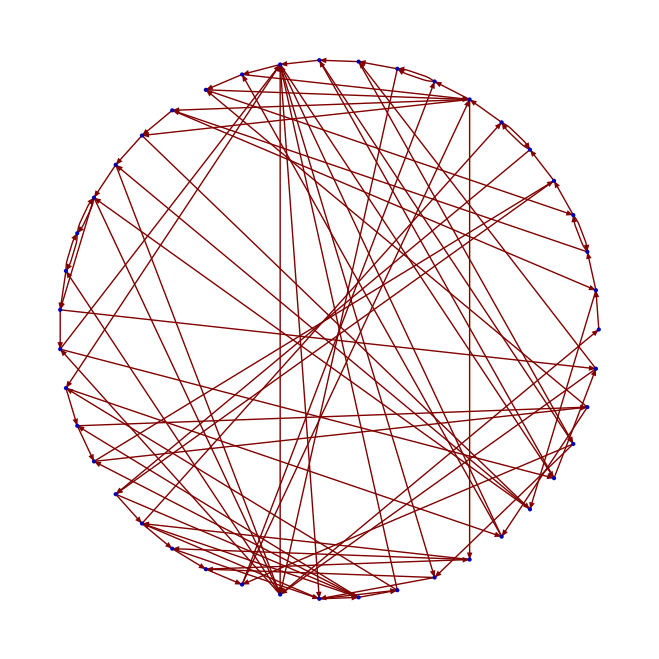
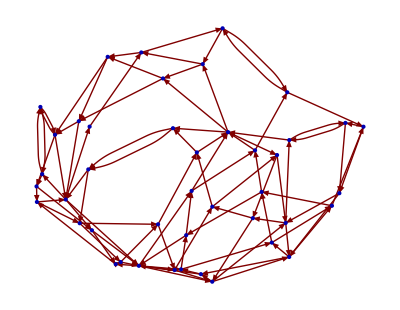
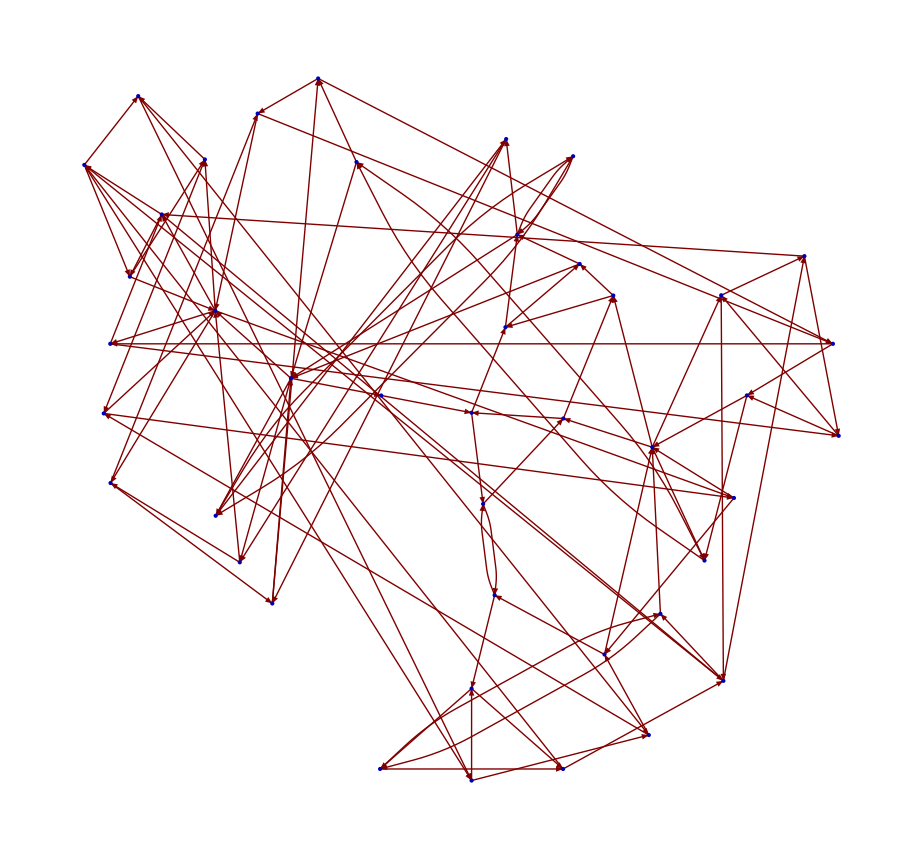
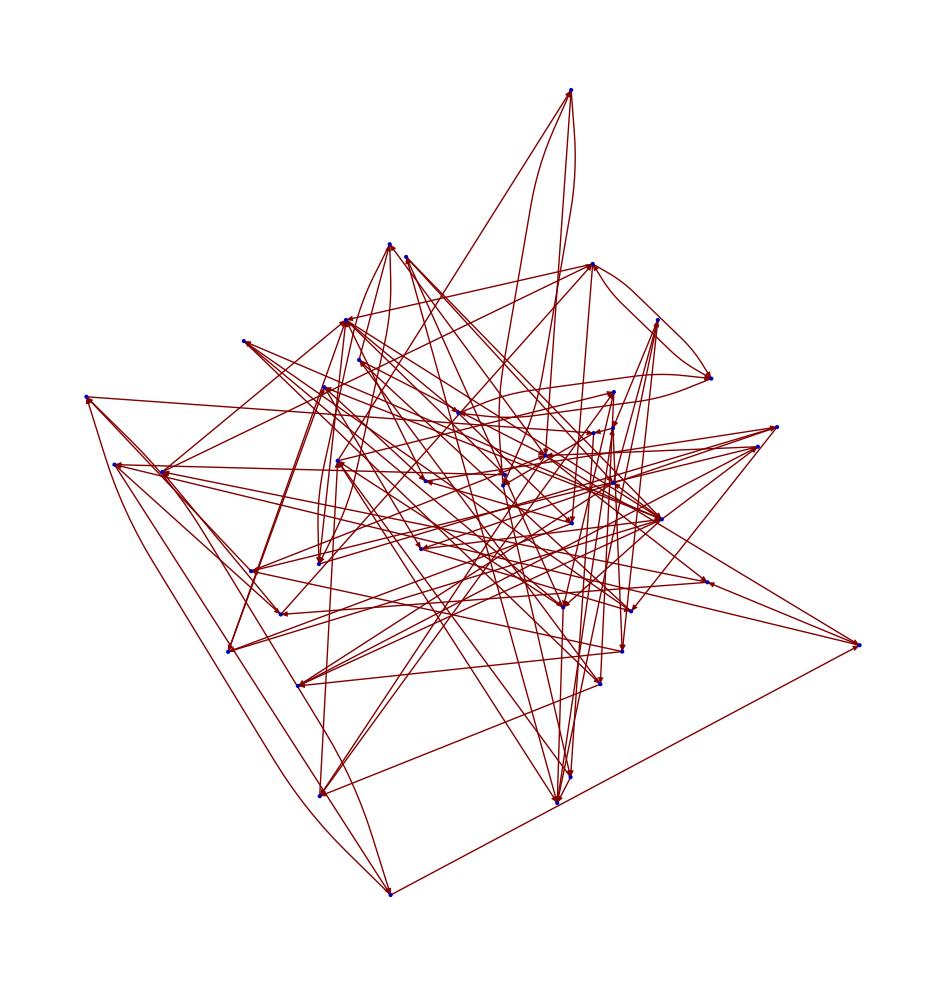
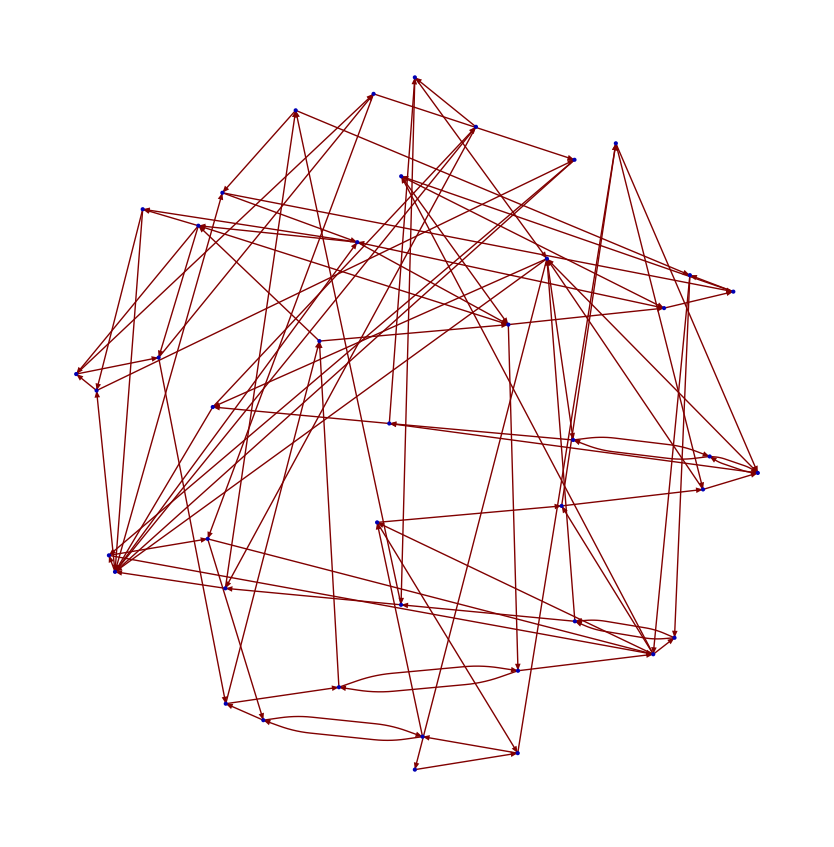
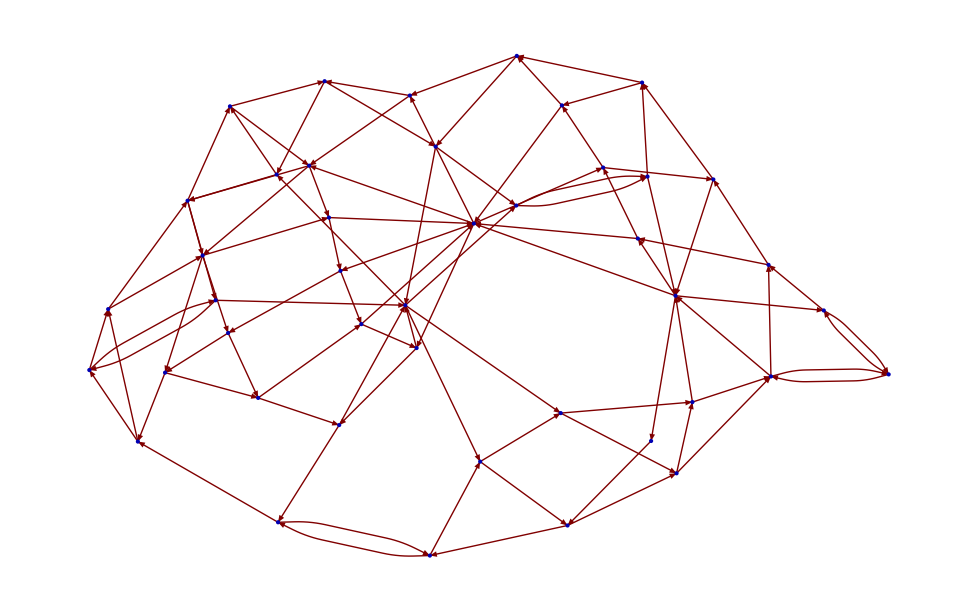
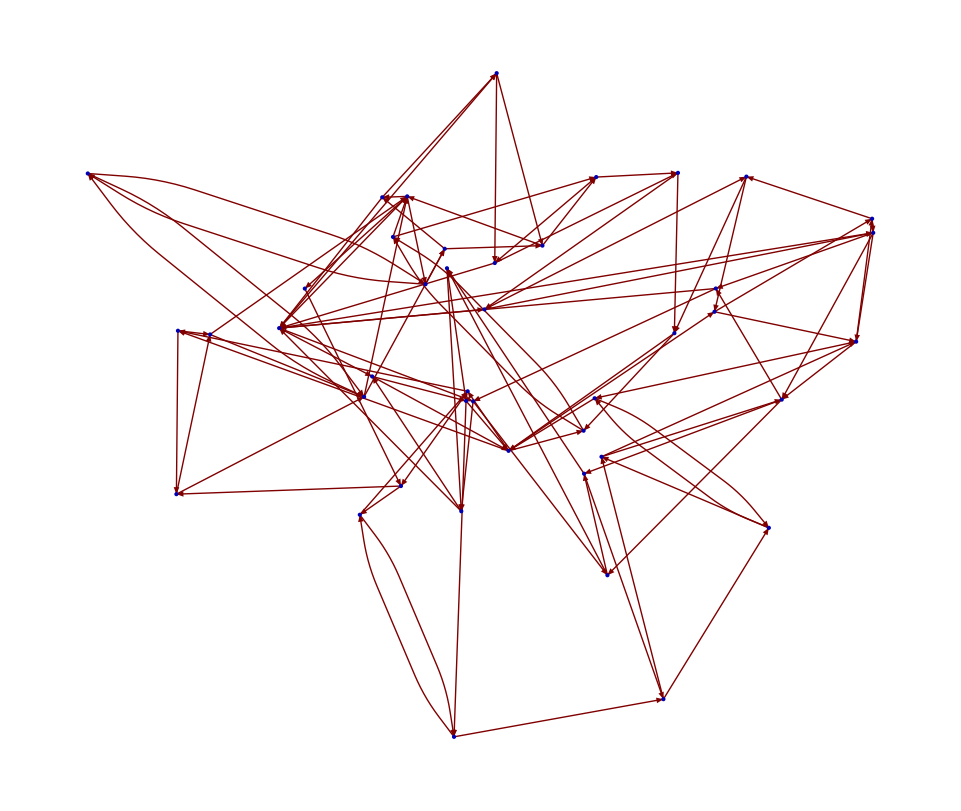

{{-Graphics3D-},{-Graphics3D- -Graphics3D-}}

```mathematica
{{GraphPlot[g,DirectedEdges->True,Method->"CircularEmbedding"]}, {GraphPlot[g,DirectedEdges->True,Method->"HighDimensionalEmbedding"]}, {GraphPlot[g,DirectedEdges->True,Method->"RadialDrawing"]}, {GraphPlot[g,DirectedEdges->True,Method->"RandomEmbedding"]}, {GraphPlot[g,DirectedEdges->True,Method->"SpiralEmbedding"]}, {GraphPlot[g,DirectedEdges->True,Method->"SpringElectricalEmbedding"]}, {GraphPlot[g,DirectedEdges->True,Method->"SpringEmbedding"]}}
{{GraphPlot3D[g]}, {GraphPlot3D[g,Method->"SpringEmbedding"]
GraphPlot3D[g,Method->"HighDimensionalEmbedding"]}}
```